# one applicable compact model v.2

## parameter

### physical parameter

```mathematica
e=1.60218 10^-19;
kB=1.38066 10^-23;
h=6.62607 10^-34;
hbar=h/(2 π);
ϵ0=8.85418 10^-12;
T=300;
m0=9.10938 10^-31;
Nav=6.02214 10^23;
```

```mathematica
nm=10^-9;
um=10^-6;
cm=10^-2;
```

```mathematica
R=2 nm;
Tox=0.5 nm;
```

```mathematica
ϵsi=11.9 ϵ0;
ϵox=3.9 ϵ0;
```

```mathematica
mt=0.19 m0;
ml=0.916 m0;
mr=2 (ml^-1+mt^-1)^-1;
```

```mathematica
mr/m0
```

0.31472

```mathematica
vt=(kB T)/e
```

0.0258522

```mathematica
wgc=0.;
wfb=0.;
```

```mathematica
Cox[r_,tox_]:=(2 π ϵox)/Log[1+tox/r]
```

### fermi-dirac integral function and its approximation

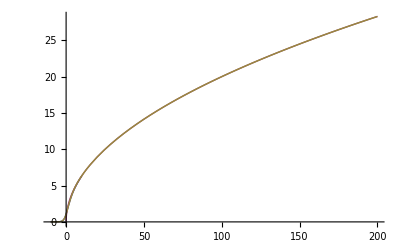

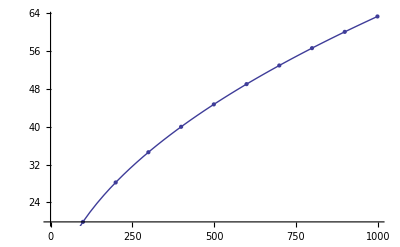

```mathematica
fermiintegral[j_,ζ_]:=-Gamma[1+j] PolyLog[1+j,-Exp[ζ]]
fermiinteralexpapp[j_,ξ_]:=Gamma[1+j] Exp[ξ]
fermiintegralappro[j_,ζ_]:=1/(j+1) ζ^(j+1)
fermiintegralaymerich[j_,ξ_]:=(((j+1) 2^(j+1))/(b+ξ+(Abs[ξ-b]^c+a^c)^(1/c))^(j+1)+Exp[-ξ]/Gamma[j+1])^-1/.a->(1+15/4 (j+1)+1/40 (j+1)^2)^(1/2)/.b->1.8+0.61 j/.c->2+(2-Sqrt[2]) 2^-j
Plot[{fermiintegral[-0.5,x],fermiintegralappro[-.5,x],fermiintegralaymerich[-.5,x]},{x,-10,200}]
Show[ListPlot[Table[{x,fermiintegralappro[-.5,x]},{x,-1,1000,100}]],Plot[fermiintegralaymerich[-.5,x],{x,-1,1000}]]
```

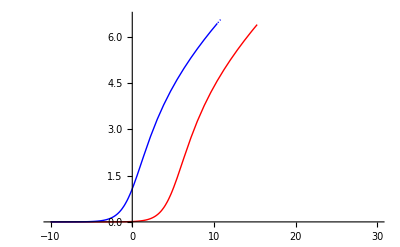

```mathematica
Plot[{fermiintegral[-.5,x-5],fermiintegral[-.5,x]},{x,-10,30},PlotStyle->{Red,Blue}]
```

```mathematica
besselenergylevel[nf_,nr_,m_,r_]:=hbar^2/(2 m) (BesselJZero[nf,nr]/r)^2(*represents the k^th zero of the Bessel function Subscript[J, n](x)*)
{{besselenergylevel[0,1,mr,R],besselenergylevel[0,1,mt,R],besselenergylevel[1,1,mr,R]}}//MatrixForm
```

(2.80425×10^-20 | 4.64501×10^-20 | 7.11924×10^-20)

```mathematica
Export["E:\\data_for_mathematica\\DeltaUgCalculation\\fermiintegral.txt",Table[{x,fermiintegralaymerich[-.5,x]},{x,-10,10,0.1}],"CSV"];
Export["E:\\data_for_mathematica\\DeltaUgCalculation\\fermiintegralseriesapprox.txt",Table[{x,fermiintegralappro[-.5,x]},{x,0,10,1}],"CSV"];
Export["E:\\data_for_mathematica\\DeltaUgCalculation\\fermiintegralexponantialapprox.txt",Table[{x,fermiinteralexpapp[-.5,x]},{x,-10,0,1}],"CSV"];
```

```mathematica
Exp[-10]
Sqrt[π]
```

1/ⅇ^10

√π

### Bessel function

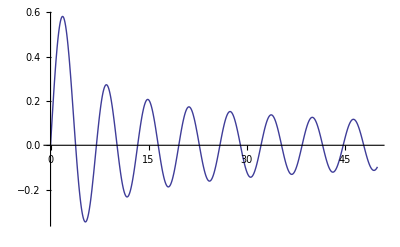

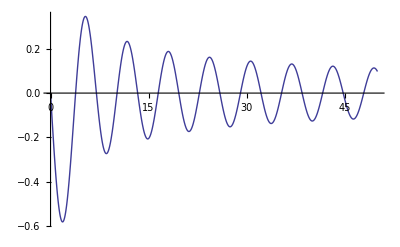

```mathematica
Plot[BesselJ[1,x],{x,0,50}]
Plot[BesselJ[-1,x],{x,0,50}]
```

```mathematica
besselelement[νf_,νr_,nf_,nr_]:=1/(2 Pi) Integrate[BesselJ[νf,BesselJZero[νf,νr] ζ]^2 ζ,{ζ,0,1}]^(-.5) Integrate[BesselJ[nf,BesselJZero[nf,nr] ζ]^2 ζ,{ζ,0,1}]^(-.5) Integrate[Exp[I (nf-νf) ϕ],{ϕ,0,2 Pi}] Integrate[BesselJ[νf,BesselJZero[νf,νr] ζ] (1-ζ^2) BesselJ[nf,BesselJZero[nf,nr] ζ] ζ,{ζ,0,1}]
```

```mathematica
valleykxky=4;
valleykz=2;
subbandtable={{valleykxky,mt/m0,besselenergylevel[0,1,mr,R]/e,besselenergylevel[0,1,mr,R]/(kB T),besselelement[0,1,0,1],0,besselenergylevel[0,1,mr,R]/e},{valleykz,ml/m0,besselenergylevel[0,1,mt,R]/e,besselenergylevel[0,1,mt,R]/(kB T),besselelement[0,1,0,1],0,besselenergylevel[0,1,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[1,1,mr,R]/e,besselenergylevel[1,1,mr,R]/(kB T),besselelement[1,1,1,1],0,besselenergylevel[1,1,mr,R]/e},{valleykz,ml/m0,besselenergylevel[1,1,mt,R]/e,besselenergylevel[1,1,mt,R]/(kB T),besselelement[1,1,1,1],0,besselenergylevel[1,1,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[0,2,mr,R]/e,besselenergylevel[0,2,mr,R]/(kB T),besselelement[0,2,0,2],0,besselenergylevel[0,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[0,2,mt,R]/e,besselenergylevel[0,2,mt,R]/(kB T),besselelement[0,2,0,2],0,besselenergylevel[0,2,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[1,2,mr,R]/e,besselenergylevel[1,2,mr,R]/(kB T),besselelement[1,2,1,2],0,besselenergylevel[1,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[1,2,mt,R]/e,besselenergylevel[1,2,mt,R]/(kB T),besselelement[1,2,1,2],0,besselenergylevel[0,2,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[2,2,mr,R]/e,besselenergylevel[2,2,mr,R]/(kB T),besselelement[2,2,2,2],0,besselenergylevel[2,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[2,2,mt,R]/e,besselenergylevel[2,2,mt,R]/(kB T),besselelement[2,2,2,2],0,besselenergylevel[2,2,mt,R]/e}}(*gnv,mc,Eq0/e,Eq0/kBT,H0xx,reflection*)
```

{{4,0.19,0.175027,6.77031,0.781943,0,0.175027},{2,0.916,0.289918,11.2145,0.781943,0,0.289918},{4,0.19,0.444347,17.188,0.666667,0,0.444347},{2,0.916,0.736026,28.4706,0.666667,0,0.736026},{4,0.19,0.922208,35.6724,0.688545,0,0.922208},{2,0.916,1.52756,59.0884,0.688545,0,1.52756},{4,0.19,1.48959,57.6195,0.666667,0,1.48959},{2,0.916,2.46738,95.4421,0.666667,0,1.52756},{4,0.19,2.14426,82.9433,0.638438,0,2.14426},{2,0.916,3.5518,137.389,0.638438,0,3.5518}}

## ΔUg numerical calculation

### lowest subband

#### defined parameter ΔUg

```mathematica
(*lowestsubbandug[vgs_,vds_,r_,tox_,st_]:=Re[FindRoot[4 Pi ϵsi U==e/(Pi hbar) Sqrt[(kB T mt)/2] st[[1,1]] (fermiintegral[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-Eq01]+fermiintegral[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-Eq01-vds/vt]) /.Eq01->st[[1,4]]+st[[1,5]] U/vt,{U,0.01}][[1,2]]]
Plot[lowestsubbandug[vgs,0.8,R,Tox,subbandtable],{vgs,-1,2}]*)
```

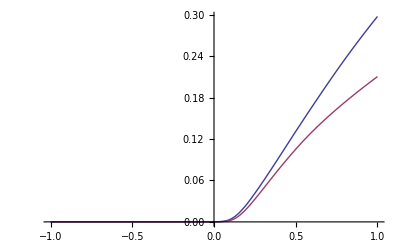

E:\data_for_mathematica\Deltaug\calculationfromfirstsubbandwithradius1nm.txt

```mathematica
lowestsubbandnumugamyrich[vgs_,vds_,r_,tox_,st_]:=Re[FindRoot[4 Pi ϵsi U==e/(Pi hbar) Sqrt[(kB T mt)/2] st[[1,1]] (fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-Eq01]+fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-Eq01-vds/vt]) /.Eq01->st[[1,4]]+st[[1,5]] U/vt,{U,0.01}][[1,2]]]
Plot[{lowestsubbandnumugamyrich[vgs,0,R,Tox,subbandtable],lowestsubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1}]
Export["E:\data_for_mathematica\Deltaug\calculationfromfirstsubbandwithradius1nm.txt",Table[{vgs,lowestsubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,3,0.1}],"CSV"]
```

### 2 subbands

Plot::exclul: {Im[Abs[-43.6547 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, « 6 », (38.6815\ Im[-1.36175\ U + vgs] + Im[-30.2467\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0} 必须是由方程或者实值函数组成的列表.

Plot::exclul: {Im[Abs[-12.7095 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, (38.6815\ Im[-1.36175\ U + vgs] + Im[-30.2467\ U + « 1 »]) - 0, « 1 », (38.6815\ Im[-1.36175\ U + vgs] + Im[-30.2467\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0} 必须是由方程或者实值函数组成的列表.

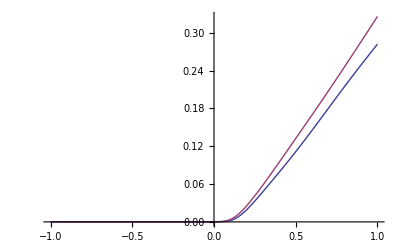

Plot::pllim: 范围指定 {vgs, -1, 1, 0.1} 不满足格式 {x, xmin, xmax}.

Show::gtype: Plot 不是一个图形类别.

Show[Plot[{lowestsubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable],twosubbandsnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1,0.1}]]

{8.93211×10^-22,9.0473×10^-22}
{4.27435×10^-20,4.32947×10^-20}
{2.04544×10^-18,2.07182×10^-18}
{9.78819×10^-17,9.91442×10^-17}
{4.68402×10^-15,4.74443×10^-15}
{2.24148×10^-13,2.27039×10^-13}
{1.07263×10^-11,1.08647×10^-11}
{5.13295×10^-10,5.19915×10^-10}
{2.45631×10^-8,2.48798×10^-8}
{1.1753×10^-6,1.19046×10^-6}
{0.0000559428,0.0000566614}
{0.00217615,0.00220076}
{0.0191893,0.0193422}
{0.0476004,0.0481121}
{0.0773635,0.0792485}
{0.105324,0.111351}
{0.130505,0.14526}
{0.152867,0.180246}
{0.173317,0.215161}
{0.192413,0.249068}
{0.210429,0.281871}

E:\data_for_mathematica\Deltaug\calculationfrom1stsubbandwithradius1nm.txt

E:\data_for_mathematica\Deltaug\numcalculationfrom2subbandwithradius1nm.txt

```mathematica
twosubbandsnumugamyrich[vgs_,vds_,r_,tox_,st_]:=Re[FindRoot[4 Pi ϵsi U==e/(Pi hbar) Sqrt[(kB T m0)/2] Sum[st[[i,1]] Sqrt[st[[i,2]]](fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-st[[i,4]]-st[[i,5]] U/vt]+fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-st[[i,4]]-st[[i,5]] U/vt-vds/vt]) ,{i,1,2}],{U,0.01}][[1,2]]]
Plot[{twosubbandsnumugamyrich[vgs,0.8,R,Tox,subbandtable],twosubbandsnumugamyrich[vgs,0,R,Tox,subbandtable],twobandinverseug[vgs],twobandUanalytcalcal[vgs,0.8,R,Tox,subbandtable] },{vgs,-1,1}]
Show[Plot[{lowestsubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable],twosubbandsnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1,0.1}]]
Column[Table[{lowestsubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable],twosubbandsnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1,0.1}]]
Export["E:\data_for_mathematica\Deltaug\calculationfrom1stsubbandwithradius1nm.txt",Table[{vgs,lowestsubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,3,0.1}],"CSV"]
Export["E:\data_for_mathematica\Deltaug\\numcalculationfrom2subbandwithradius1nm.txt",Table[{vgs,twosubbandsnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,3,0.1}],"CSV"]
```

```mathematica
Export["E:\data_for_mathematica\Deltaug\Acalculationfromfirstsubbandwithradius1nm.txt",Table[{vgs,4 Pi ϵsi lowestsubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable],4 Pi ϵsi twosubbandsnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,3,0.01}],"CSV"]
```

E:\data_for_mathematica\Deltaug\Acalculationfromfirstsubbandwithradius1nm.txt

## numerical ID-VG characteristic

### lowest subband

FindRoot::nlnum: 在 {U} = {0.01} 处，函数值 {1.32405×10^-11 - 3.66231×10^-11\ (1/0.56419\ Power[« 2 »] + 0.707107\ Power[« 2 »] + 1/0.56419\ Power[« 2 »] + 0.707107\ Power[« 2 »])} 不是由数字组成的维度为 {1} 的列表.

General::stop: 在本次计算中，FindRoot :: nlnum 的进一步输出将被抑制.

Plot::exclul: {Im[ⅇ^-37.7155 + 38.6815\ (0.  + vgs + Times[« 2 »]) - 30.2467\ Re[Rule[« 2 »]]] - 0, Im[ⅇ^-6.77031 + 38.6815\ (0.  + vgs + Times[« 2 »]) - 30.2467\ Re[Rule[« 2 »]]] - 0} 必须是由方程或者实值函数组成的列表.

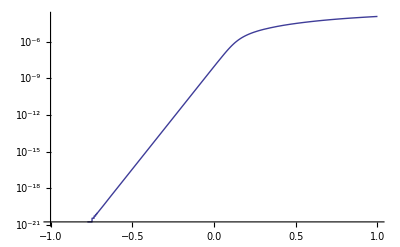

E:\data_for_mathematica\current\numculationofcurrentfrom1stsubbandwithradius1nm.txt

E:\data_for_mathematica\current\numculationofcurrentfrom1stsubbandwithradius1nm_ua.txt

```mathematica
lowestsubbandnumids[vgs_,vds_,r_,tox_,st_]:=  (e kB T)/(Pi hbar) st[[1,1]] (Log[1+Exp[1/vt(vgs-wgc+wfb-(4 Pi ϵsi lowestsubbandnumugamyrich[vgs,vds,r,tox,st])/Cox[r,tox])-st[[1,4]]-st[[1,5]]/vt lowestsubbandnumugamyrich[vgs,vds,r,tox,st]]]-Log[1+Exp[1/vt(vgs-wgc+wfb-(4 Pi ϵsi lowestsubbandnumugamyrich[vgs,vds,r,tox,st])/Cox[r,tox])-st[[1,4]]-st[[1,5]]/vt lowestsubbandnumugamyrich[vgs,vds,r,tox,st]-vds/vt]])
LogPlot[lowestsubbandnumids[vgs,0.8,R,Tox,subbandtable],{vgs,-1,1}]
Export["E:\data_for_mathematica\current\\numculationofcurrentfrom1stsubbandwithradius1nm.txt",Table[{vgs,idswithtwobandsana[vgs,0.8]},{vgs,-1,3,0.1}],"CSV"]
Export["E:\data_for_mathematica\current\\numculationofcurrentfrom1stsubbandwithradius1nm_ua.txt",Table[{vgs,10^6 idswithtwobandsana[vgs,0.8]},{vgs,-1,3,0.1}],"CSV"]
```

### 2 subbands

Plot::exclul: {Im[Abs[-43.6547 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, (38.6815\ Im[-1.36175\ U + vgs] + Im[-30.2467\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0, « 48 », « 18 »} 必须是由方程或者实值函数组成的列表.

Plot::exclul: {Im[ⅇ^-37.7155 + 38.6815\ (0.  + vgs + Times[« 2 »]) - 30.2467\ Re[Rule[« 2 »]]] - 0, Im[ⅇ^-6.77031 + 38.6815\ (0.  + vgs + Times[« 2 »]) - 30.2467\ Re[Rule[« 2 »]]] - 0} 必须是由方程或者实值函数组成的列表.

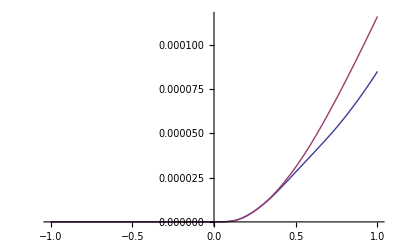

{-1.,0.,0.,0.}
{-0.95,0.,0.,0.}
{-0.9,0.,0.,0.}
{-0.85,0.,0.,0.}
{-0.8,0.,0.,0.}
{-0.75,1.77907×10^-21,1.77907×10^-21,1.77907×10^-21}
{-0.7,1.60116×10^-20,1.60116×10^-20,1.60116×10^-20}
{-0.65,1.11192×10^-19,1.10302×10^-19,1.11192×10^-19}
{-0.6,7.69449×10^-19,7.65001×10^-19,7.69449×10^-19}
{-0.55,5.32743×10^-18,5.2963×10^-18,5.32743×10^-18}
{-0.5,3.68481×10^-17,3.66329×10^-17,3.68481×10^-17}
{-0.45,2.54897×10^-16,2.53409×10^-16,2.54897×10^-16}
{-0.4,1.76329×10^-15,1.75299×10^-15,1.76329×10^-15}
{-0.35,1.21978×10^-14,1.21265×10^-14,1.21978×10^-14}
{-0.3,8.43798×10^-14,8.38871×10^-14,8.43798×10^-14}
{-0.25,5.83709×10^-13,5.80301×10^-13,5.83709×10^-13}
{-0.2,4.03788×10^-12,4.01431×10^-12,4.03788×10^-12}
{-0.15,2.79323×10^-11,2.77692×10^-11,2.79323×10^-11}
{-0.1,1.93207×10^-10,1.92079×10^-10,1.93207×10^-10}
{-0.05,1.33566×10^-9,1.32788×10^-9,1.33566×10^-9}
{0.,9.19815×10^-9,9.14495×10^-9,9.19815×10^-9}
{0.05,6.17464×10^-8,6.14084×10^-8,6.17464×10^-8}
{0.1,3.60543×10^-7,3.59107×10^-7,3.60543×10^-7}
{0.15,1.40378×10^-6,1.40281×10^-6,1.40378×10^-6}
{0.2,3.42379×10^-6,3.43426×10^-6,3.42379×10^-6}
{0.25,6.25681×10^-6,6.30339×10^-6,6.25681×10^-6}
{0.3,9.73958×10^-6,9.87081×10^-6,9.73958×10^-6}
{0.35,0.0000137728,0.0000140982,0.0000137728}
{0.4,0.0000183502,0.0000191006,0.0000183502}
{0.45,0.0000232305,0.0000247373,0.0000232305}
{0.5,0.0000281616,0.0000309126,0.0000281616}
{0.55,0.0000330701,0.0000376798,0.0000330701}
{0.6,0.0000379763,0.0000450333,0.0000379763}
{0.65,0.000042935,0.0000528888,0.000042935}
{0.7,0.0000480064,0.0000611437,0.0000480064}
{0.75,0.000053276,0.0000697149,0.000053276}
{0.8,0.0000588919,0.0000785459,0.0000588919}
{0.85,0.0000648949,0.0000875998,0.0000648949}
{0.9,0.0000712218,0.000096851,0.0000712218}
{0.95,0.0000778663,0.000106281,0.0000778663}
{1.,0.0000848784,0.000115874,0.0000848784}
{1.05,0.0000922944,0.000125618,0.0000922944}
{1.1,0.000100114,0.000135503,0.000100114}
{1.15,0.000108309,0.000145517,0.000108309}
{1.2,0.000116838,0.000155653,0.000116838}
{1.25,0.000125664,0.000165902,0.000125664}
{1.3,0.000134753,0.000176256,0.000134753}
{1.35,0.000144079,0.000186703,0.000144079}
{1.4,0.000153623,0.000197216,0.000153623}
{1.45,0.00016337,0.000207711,0.00016337}
{1.5,0.000173309,0.000217913,0.000173309}
{1.55,0.00018343,0.000227103,0.00018343}
{1.6,0.000193724,0.000234302,0.000193724}
{1.65,0.000204186,0.000239259,0.000204186}
{1.7,0.000214807,0.0002425,0.000214807}
{1.75,0.000225583,0.000244593,0.000225583}
{1.8,0.000236506,0.000245931,0.000236506}
{1.85,0.00024757,0.000246784,0.00024757}
{1.9,0.000258769,0.000247306,0.000258769}
{1.95,0.00027009,0.000247606,0.00027009}
{2.,0.00028151,0.00024777,0.00028151}

E:\data_for_mathematica\current\numericalcalculationofcurrent2subbandwithradius1nm.txt

E:\data_for_mathematica\current\numericalcalculationofcurrent2subbandwithradius1nm_ua.txt

```mathematica
towsubbandsnumids[vgs_,vds_,r_,tox_,st_]:=Re[(e kB T)/(Pi hbar) Sum[st[[i,1]] (Log[1+Exp[1/vt(vgs-wgc+wfb-(4 Pi ϵsi twosubbandsnumugamyrich[vgs,vds,r,tox,st])/Cox[r,tox])-st[[i,4]]-st[[i,5]]/vt twosubbandsnumugamyrich[vgs,vds,r,tox,st]]]-Log[1+Exp[1/vt(vgs-wgc+wfb-(4 Pi ϵsi twosubbandsnumugamyrich[vgs,vds,r,tox,st])/Cox[r,tox])-st[[i,4]]-st[[i,5]]/vt twosubbandsnumugamyrich[vgs,vds,r,tox,st]-vds/vt]]),{i,1,2}]]
DrainCurrentAymerich[vgs_,vds_,r_,tox_,st_]:=Re[(e kB T)/(π hbar) Sum[st[[i,1]]  (Log[1+Exp[(vgs-wgc+wfb-(4 π ϵsi)/Cox[R,Tox] DeltaU)/vt-(st[[i,4]]+st[[i,5]] DeltaU/vt)]]-Log[1+Exp[(vgs-wgc+wfb-(4 π ϵsi)/Cox[R,Tox] DeltaU)/vt-(st[[i,4]]+st[[i,5]] DeltaU/vt)-vds/vt]])/.DeltaU->twosubbandsnumugamyrich[vgs,vds,r,tox,st],{i,1,2}]]
Plot[{towsubbandsnumids[vgs,0.8,R,Tox,subbandtable],lowestsubbandnumids[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1}]
Column[Table[{vgs,towsubbandsnumids[vgs,0.8,R,Tox,subbandtable],lowestsubbandnumids[vgs,0.8,R,Tox,subbandtable],DrainCurrentAymerich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,2,0.05}]]
Export["E:\data_for_mathematica\current\\numericalcalculationofcurrent2subbandwithradius1nm.txt",Table[{vgs,DrainCurrentAymerich[vgs, 0.8, R, Tox, subbandtable]},{vgs,-1,3,0.1}],"CSV"]
Export["E:\data_for_mathematica\current\\numericalcalculationofcurrent2subbandwithradius1nm_ua.txt",Table[{vgs,10^6 DrainCurrentAymerich[vgs, 0.8, R, Tox, subbandtable]},{vgs,-1,3,0.1}],"CSV"]
```

### the lowest subband with 2 subbands

Plot::exclul: {Im[Abs[-43.6547 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, (38.6815\ Im[-1.36175\ U + vgs] + Im[-30.2467\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0, « 48 », « 18 »} 必须是由方程或者实值函数组成的列表.

Plot::exclul: {Im[ⅇ^-37.7155 + 38.6815\ (0.  + vgs + Times[« 2 »]) - 30.2467\ Re[Rule[« 2 »]]] - 0, Im[ⅇ^-6.77031 + 38.6815\ (0.  + vgs + Times[« 2 »]) - 30.2467\ Re[Rule[« 2 »]]] - 0} 必须是由方程或者实值函数组成的列表.

Plot::exclul: {Im[Abs[-43.6547 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, « 32 », Im[ⅇ^-6.77031 + 38.6815\ (0.  + vgs + Times[« 2 »]) - 6.35327×10^-10\ Re[Plus[« 2 »]]] - 0} 必须是由方程或者实值函数组成的列表.

General::stop: 在本次计算中，Plot :: exclul 的进一步输出将被抑制.

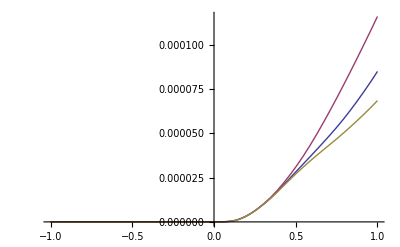

{-1.,0.,0.,0.,0.}
{-0.95,0.,0.,0.,0.}
{-0.9,0.,0.,0.,0.}
{-0.85,0.,0.,0.,0.}
{-0.8,0.,0.,0.,0.}
{-0.75,1.77907×10^-21,1.77907×10^-21,1.77907×10^-21,1.77907×10^-21}
{-0.7,1.60116×10^-20,1.60116×10^-20,1.60116×10^-20,1.60116×10^-20}
{-0.65,1.11192×10^-19,1.10302×10^-19,1.11192×10^-19,1.10302×10^-19}
{-0.6,7.69449×10^-19,7.65001×10^-19,7.69449×10^-19,7.65001×10^-19}
{-0.55,5.32743×10^-18,5.2963×10^-18,5.32743×10^-18,5.2963×10^-18}
{-0.5,3.68481×10^-17,3.66329×10^-17,3.68481×10^-17,3.66329×10^-17}
{-0.45,2.54897×10^-16,2.53409×10^-16,2.54897×10^-16,2.53409×10^-16}
{-0.4,1.76329×10^-15,1.75299×10^-15,1.76329×10^-15,1.75299×10^-15}
{-0.35,1.21978×10^-14,1.21265×10^-14,1.21978×10^-14,1.21265×10^-14}
{-0.3,8.43798×10^-14,8.38871×10^-14,8.43798×10^-14,8.38871×10^-14}
{-0.25,5.83709×10^-13,5.80301×10^-13,5.83709×10^-13,5.80301×10^-13}
{-0.2,4.03788×10^-12,4.01431×10^-12,4.03788×10^-12,4.01431×10^-12}
{-0.15,2.79323×10^-11,2.77692×10^-11,2.79323×10^-11,2.77692×10^-11}
{-0.1,1.93207×10^-10,1.92079×10^-10,1.93207×10^-10,1.92079×10^-10}
{-0.05,1.33566×10^-9,1.32788×10^-9,1.33566×10^-9,1.32786×10^-9}
{0.,9.19815×10^-9,9.14495×10^-9,9.19815×10^-9,9.14441×10^-9}
{0.05,6.17464×10^-8,6.14084×10^-8,6.17464×10^-8,6.13845×10^-8}
{0.1,3.60543×10^-7,3.59107×10^-7,3.60543×10^-7,3.58391×10^-7}
{0.15,1.40378×10^-6,1.40281×10^-6,1.40378×10^-6,1.39484×10^-6}
{0.2,3.42379×10^-6,3.43426×10^-6,3.42379×10^-6,3.399×10^-6}
{0.25,6.25681×10^-6,6.30339×10^-6,6.25681×10^-6,6.20219×10^-6}
{0.3,9.73958×10^-6,9.87081×10^-6,9.73958×10^-6,9.63154×10^-6}
{0.35,0.0000137728,0.0000140982,0.0000137728,0.0000135692}
{0.4,0.0000183502,0.0000191006,0.0000183502,0.0000179723}
{0.45,0.0000232305,0.0000247373,0.0000232305,0.0000225528}
{0.5,0.0000281616,0.0000309126,0.0000281616,0.0000270175}
{0.55,0.0000330701,0.0000376798,0.0000330701,0.0000312637}
{0.6,0.0000379763,0.0000450333,0.0000379763,0.0000352997}
{0.65,0.000042935,0.0000528888,0.000042935,0.0000391836}
{0.7,0.0000480064,0.0000611437,0.0000480064,0.0000429874}
{0.75,0.000053276,0.0000697149,0.000053276,0.0000468026}
{0.8,0.0000588919,0.0000785459,0.0000588919,0.0000507592}
{0.85,0.0000648949,0.0000875998,0.0000648949,0.0000549051}
{0.9,0.0000712218,0.000096851,0.0000712218,0.0000592153}
{0.95,0.0000778663,0.000106281,0.0000778663,0.0000637021}
{1.,0.0000848784,0.000115874,0.0000848784,0.0000684112}

E:\data_for_mathematica\numericalcalculationofcurrenttwosubbandwithradius1nm.txt

```mathematica
lowestonetowsubbandsnumids[vgs_,vds_,r_,tox_,st_]:=Re[(e kB T)/(Pi hbar) st[[1,1]] (Log[1+Exp[1/vt(vgs-wgc+wfb-(4 Pi ϵsi twosubbandsnumugamyrich[vgs,vds,r,tox,st])/Cox[r,tox])-st[[1,4]]-st[[1,5]]/vt twosubbandsnumugamyrich[vgs,vds,r,tox,st]]]-Log[1+Exp[1/vt(vgs-wgc+wfb-(4 Pi ϵsi twosubbandsnumugamyrich[vgs,vds,r,tox,st])/Cox[r,tox])-st[[1,4]]-st[[1,5]]/vt twosubbandsnumugamyrich[vgs,vds,r,tox,st]-vds/vt]])]
lowestoneDrainCurrentAymerich[vgs_,vds_,r_,tox_,st_]:=Re[(e kB T)/(π hbar) Sum[st[[1,1]]  (Log[1+Exp[(vgs-wgc+wfb-(4 π ϵsi)/Cox[R,Tox] DeltaU)/vt-(st[[i,4]]+st[[i,5]] DeltaU/vt)]]-Log[1+Exp[(vgs-wgc+wfb-(4 π ϵsi)/Cox[R,Tox] DeltaU)/vt-(st[[i,4]]+st[[i,5]] DeltaU/vt)-vds/vt]])/.DeltaU->twosubbandsnumugamyrich[vgs,vds,r,tox,st],{i,1,1}]]
Plot[{towsubbandsnumids[vgs,0.8,R,Tox,subbandtable],lowestsubbandnumids[vgs,0.8,R,Tox,subbandtable],lowestonetowsubbandsnumids[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1}]
Column[Table[{vgs,towsubbandsnumids[vgs,0.8,R,Tox,subbandtable],lowestsubbandnumids[vgs,0.8,R,Tox,subbandtable],DrainCurrentAymerich[vgs,0.8,R,Tox,subbandtable],lowestonetowsubbandsnumids[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1,0.05}]]
Export["E:\data_for_mathematica\\numericalcalculationofcurrenttwosubbandwithradius1nm.txt",Table[{vgs,DrainCurrentAymerich[vgs, 0.8, R, Tox, subbandtable]},{vgs,-1,3,0.1}],"CSV"]
```

## check

Plot::exclul: {Im[Abs[-43.6547 + 38.6815\ Plus[« 3 »] - 30.2467\ U]^2.82843] - 0, (38.6815\ Im[P - 1.36175\ U] + Im[-30.2467\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0, « 48 », « 18 »} 必须是由方程或者实值函数组成的列表.

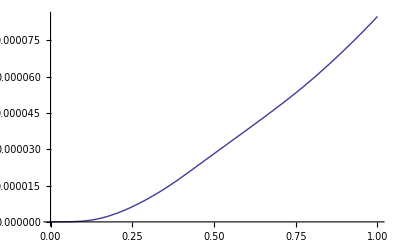

```mathematica
p[P_]:=(e kB T)/(π hbar) Sum[subbandtable[[i,1]] (Log[1+Exp[1/vt(P-wgc+wfb-(4 Pi ϵsi twosubbandsnumugamyrich[P,0.8,R,Tox,subbandtable])/Cox[R,Tox])-subbandtable[[i,4]]-subbandtable[[i,5]]/vt twosubbandsnumugamyrich[P,0.8,R,Tox,subbandtable]]]-Log[1+Exp[1/vt(P-wgc+wfb-(4 Pi ϵsi twosubbandsnumugamyrich[P,0.8,R,Tox,subbandtable])/Cox[R,Tox])-subbandtable[[i,4]]-subbandtable[[i,5]]/vt twosubbandsnumugamyrich[P,0.8,R,Tox,subbandtable]-0.8/vt]]),{i,1,2}]
Plot[p[P],{P,0,1}]
```

```mathematica
pp[Vgs_]:=(e kB T)/(π hbar) subbandtable[[l,1]] (Log[1+Exp[1/vt(Vgs-wgc+wfb-(4 Pi ϵsi twosubbandsnumugamyrich[Vgs,0.8,R,Tox,subbandtable])/Cox[R,Tox])-subbandtable[[i,4]]-subbandtable[[i,5]]/vt twosubbandsnumugamyrich[Vgs,0.8,R,Tox,subbandtable]]]-Log[1+Exp[1/vt(Vgs-wgc+wfb-(4 Pi ϵsi twosubbandsnumugamyrich[Vgs,0.8,R,Tox,subbandtable])/Cox[R,Tox])-subbandtable[[i,4]]-subbandtable[[i,5]]/vt twosubbandsnumugamyrich[Vgs,0.8,R,Tox,subbandtable]-0.8/vt]])/.l->1

ppp[Vgs_]:=(e kB T)/(π hbar) subbandtable[[l,1]] (Log[1+Exp[1/vt(Vgs-wgc+wfb-(4 Pi ϵsi twosubbandsnumugamyrich[Vgs,0.8,R,Tox,subbandtable])/Cox[R,Tox])-subbandtable[[i,4]]-subbandtable[[i,5]]/vt twosubbandsnumugamyrich[Vgs,0.8,R,Tox,subbandtable]]]-Log[1+Exp[1/vt(Vgs-wgc+wfb-(4 Pi ϵsi twosubbandsnumugamyrich[Vgs,0.8,R,Tox,subbandtable])/Cox[R,Tox])-subbandtable[[i,4]]-subbandtable[[i,5]]/vt twosubbandsnumugamyrich[Vgs,0.8,R,Tox,subbandtable]-0.8/vt]])/.l->2
Show[Plot[p[P],{P,0,1}],Plot[{pp[Vgs],ppp[Vgs]},{Vgs,0,1}]]
```

Plot::exclul: {Im[Abs[-43.6547 + 38.6815\ Plus[« 3 »] - 30.2467\ U]^2.82843] - 0, (38.6815\ Im[P - 1.36175\ U] + Im[-30.2467\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0, « 48 », « 18 »} 必须是由方程或者实值函数组成的列表.

Part::pspec: 部分指定 l 既不是一个机器精度整数，也不是由机器精度整数组成的列表.

Part::pspec: 部分指定 i 既不是一个机器精度整数，也不是由机器精度整数组成的列表.

General::stop: 在本次计算中，Part :: pspec 的进一步输出将被抑制.

-Graphics-

## ΔUg analytic calculation

### single band

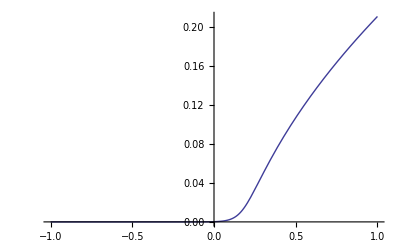

{{-1.,3.23992×10^-15},{-0.95,1.1382×10^-14},{-0.9,3.96961×10^-14},{-0.85,1.38612×10^-13},{-0.8,4.83819×10^-13},{-0.75,1.68865×10^-12},{-0.7,5.89401×10^-12},{-0.65,2.05721×10^-11},{-0.6,7.18038×10^-11},{-0.55,2.5062×10^-10},{-0.5,8.74749×10^-10},{-0.45,3.05318×10^-9},{-0.4,1.06566×10^-8},{-0.35,3.71953×10^-8},{-0.3,1.29824×10^-7},{-0.25,4.53125×10^-7},{-0.2,1.58151×10^-6},{-0.15,5.51933×10^-6},{-0.1,0.0000192562},{-0.05,0.000067112},{0.,0.00023305},{0.05,0.000799287},{0.1,0.00263322},{0.15,0.00775772},{0.2,0.0183293},{0.25,0.0332745},{0.3,0.0494605},{0.35,0.0651364},{0.4,0.0798731},{0.45,0.0936953},{0.5,0.10672},{0.55,0.11906},{0.6,0.130812},{0.65,0.142051},{0.7,0.152839},{0.75,0.163226},{0.8,0.173253},{0.85,0.182957},{0.9,0.192365},{0.95,0.201505},{1.,0.210396},{1.05,0.219059},{1.1,0.227511},{1.15,0.235765},{1.2,0.243836},{1.25,0.251735},{1.3,0.259472},{1.35,0.267057},{1.4,0.2745},{1.45,0.281806},{1.5,0.288984},{1.55,0.296041},{1.6,0.302981},{1.65,0.309812},{1.7,0.316537},{1.75,0.323161},{1.8,0.32969},{1.85,0.336126},{1.9,0.342474},{1.95,0.348738},{2.,0.35492},{2.05,0.361024},{2.1,0.367052},{2.15,0.373007},{2.2,0.378893},{2.25,0.384711},{2.3,0.390463},{2.35,0.396152},{2.4,0.40178},{2.45,0.407349},{2.5,0.41286},{2.55,0.418315},{2.6,0.423717},{2.65,0.429065},{2.7,0.434363},{2.75,0.439612},{2.8,0.444812},{2.85,0.449965},{2.9,0.455073},{2.95,0.460136},{3.,0.465156}}

E:\data_for_mathematica\Deltaug\calculationfrom1stsubwithradius1nm_a.txt

E:\data_for_mathematica\Deltaug\calculationfromfirstsubwithradius1nm_inversion.txt

E:\data_for_mathematica\Deltaug\calculationfrom1stsubwithradius1nm_subthresh.txt

```mathematica
allregionuga[vgs_] := 
 b/(2 a) (-1 + Sqrt[1 + (4 a)/(b b) 1/25 Log[1 + Exp[25 (vgs + c)]]]) /. 
    a -> (8 Pi^4 hbar^2 ϵsi^2)/(subbandtable[[1, 1]]^2 e^3 mt) /. 
   b -> subbandtable[[1, 5]] + (4 Pi ϵsi)/Cox[R, Tox] /. 
  c -> -wgc + wfb - subbandtable[[1, 3]]
inversion[vgs_]:= b/(2 a) (-1 + Sqrt[1 + (4 a)/(b b) (vgs + c)]) /. 
    a -> (8 Pi^4 hbar^2 ϵsi^2)/(subbandtable[[1, 1]]^2 e^3 mt) /. 
   b -> subbandtable[[1, 5]] + (4 Pi ϵsi)/Cox[R, Tox] /. 
  c -> -wgc + wfb - subbandtable[[1, 3]]
Plot[allregionuga[vgs], {vgs, -1, 1}]
Table[{vgs, allregionuga[vgs]}, {vgs, -1, 3, 0.05}]
Export["E:\data_for_mathematica\Deltaug\calculationfrom1stsubwithradius1nm_a.txt",Table[{vgs,allregionuga[vgs] },{vgs,-1,3,0.05}],"CSV"]
Export["E:\data_for_mathematica\Deltaug\calculationfromfirstsubwithradius1nm_inversion.txt",Table[{vgs, Re[inversion[vgs]]},{vgs,-1,3,0.05}],"CSV"]
Export["E:\data_for_mathematica\Deltaug\calculationfrom1stsubwithradius1nm_subthresh.txt",Table[{vgs, 0},{vgs,-1,0,0.05}],"CSV"]
```

```mathematica
(8 Pi^4 hbar^2 ϵsi^2)/(subbandtable[[1, 1]]^2 e^3 mt)
subbandtable[[1, 5]] + (4 Pi ϵsi)/Cox[R, Tox]
(4 Pi ϵsi)/Cox[R, Tox]
-wgc + wfb - subbandtable[[1, 3]]
```

8.44765

2.14369

1.36175

-0.175027

### calculation from Uno

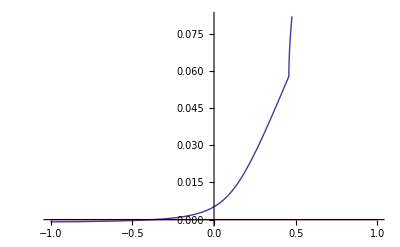

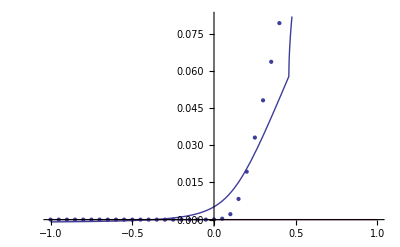

E:\data_for_mathematica\Deltaug\calculationfromUNOwithradius1nm.txt

```mathematica
twobandUanalytcalcal[vgs_,vds_,r_,tox_,st_]:=Re[vt (-(d1/4)+1/2 √(d1^2/2-(4 d2)/3-k1/(3 k3)-k3/3+(-d1^3+4 d1 d2-8 d3)/(4 Sqrt[k4]))+Sqrt[k4]/2)]/.k4->d1^2/4-(2 d2)/3+k1/(3 k3)+k3/3/.k3->((k2+Sqrt[-4 k1^3+k2^2])/2)^(1/3)/.k2->2 d2^3-9 d1 d2 d3+27 d3^2+27 d1^2 d4-72 d2 d4/.k1->d2^2-3 d1 d3+12 d4/.d1->(2 b2)/b1/.d2->(b2^2-2 b1 b3-b4^2 b7)/b1^2/.d3->(-2 b2 b3+b4^2 b6)/b1^2/.d4->(b3^2-b4^2 b5)/b1^2/.b1->c1^2/.b2->(c2+h00) c40^2+(c2+h11) c41^2/.b3->c30 c40^2+c31 c41^2/.b4->2 c40 c41/.b5->c30 c31/.b6->(c2+h11) c30+(c2+h00) c31/.b7->(c2+h00) (c2+h11)/.c1->(4 π^2 hbar ϵsi)/e^2 Sqrt[(kB T)/(2 m0)]/.c2->(4 π ϵsi)/Cox[r,tox]/.c30->(vgs-wgc+wfb)/vt-subbandtable[[1,4]]/.c31->(vgs-wgc+wfb)/vt-subbandtable[[2,4]]/.c40->subbandtable[[1,1]] Sqrt[subbandtable[[1,2]]] (1+subbandtable[[1,6]])/.c41->subbandtable[[2,1]] Sqrt[subbandtable[[2,2]]] (1+subbandtable[[2,6]])/.h00->subbandtable[[1,5]]/.h11->subbandtable[[2,5]]
FuncDeltaUParabolicPotentialAnalyticTwoSubbandStrongInversion02[VGS_,VDS_,R_,Tox_,tablesubband_]:=vt (-d1/4+1/2 √(d1^2/2-(4 d2)/3-k1/(3 k3)-k3/3+(-d1^3+4 d1 d2-8 d3)/(4 √k4))+(√k4)/2)/.k4->d1^2/4-(2 d2)/3+k1/(3 k3)+k3/3/.k3->((k2+√(-4 k1^3+k2^2))/2)^(1/3)/.k2->2 d2^3-9 d1 d2 d3+27 d3^2+27 d1^2 d4-72 d2 d4/.k1->d2^2-3 d1 d3+12 d4/.d1->(2 b2)/b1/.d2->(b2^2-2b1 b3-b4^2 b7)/b1^2/.d3->0/.d4->0/.b1->c1^2/.b2->(c2+h00)c40^2+(c2+h11)c41^2/.b3->c30 c40^2+c31 c41^2/.b4->2 c40 c41/.b5->c30 c31/.b6->(c2+h11)c30+(c2+h00)c31/.b7->(c2+h00)(c2+h11)/.c1->(4 π^2 hbar ϵsi)/e^2 Sqrt[(kB T)/(2m0)]/.c2->(4 π ϵsi)/Cox[R,Tox]/.c30->(VGS-wgc+wfb)/vt-subbandtable[[1,4]]/vt/.c31->(VGS-wgc+wfb)/vt-subbandtable[[2,4]]/vt/.c40->subbandtable[[1,1]]Sqrt[subbandtable[[1,2]]](1+subbandtable[[1,6]])/.c41->subbandtable[[2,1]]Sqrt[subbandtable[[2,2]]](1+subbandtable[[2,6]])/.h00->subbandtable[[1,5]]/.h11->subbandtable[[2,5]]
Plot[{twobandUanalytcalcal[vgs,0.8,R,Tox,subbandtable],FuncDeltaUParabolicPotentialAnalyticTwoSubbandStrongInversion02[vgs,0.8,R,Tox,subbandtable]}, {vgs, -1, 1}]
Show[Plot[{twobandUanalytcalcal[vgs,0.8,R,Tox,subbandtable],FuncDeltaUParabolicPotentialAnalyticTwoSubbandStrongInversion02[vgs,0.8,R,Tox,subbandtable]}, {vgs, -1, 1}], ListPlot[Table[{vgs,twosubbandsnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,3,0.05}]]]
Export["E:\data_for_mathematica\Deltaug\calculationfromUNOwithradius1nm.txt",Table[{vgs,twobandUanalytcalcal[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,3,0.05}],"CSV"]
```

### calculation from me

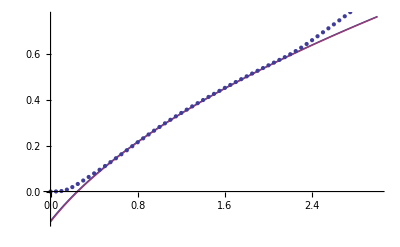

E:\data_for_mathematica\Deltaug\calculationfrom2ndsubbandwithradius1nm.txt

```mathematica
twobandinverseug[vgs_] := 
 Re[vt 1/2 (-d1 + Sqrt[d1^2 - 4 d2])] /. d1 -> 2 b2/b1 /. 
               d2 -> (b2^2 - 2 b1 b3 - b4^2 b7)/b1^2 /.b1 -> c1^2 /. 
             b2 -> (c2 + h00) c40^2 + (c2 + h11) c41^2 /. 
            b3 -> c30 c40^2 + c31 c41^2 /. b4 -> 2 c40 c41 /. 
          b7 -> (c2 + h00) (c2 + h11) /. 
         c1 -> 4 Pi^2 hbar ϵsi/e^2 Sqrt[(kB T)/(2 m0)] /. 
        c2 -> (4 Pi ϵsi)/Cox[R, Tox] /. 
       c30 -> (vgs - wgc + wfb)/vt - subbandtable[[1, 4]] /. 
      c31 -> (vgs - wgc + wfb)/vt - subbandtable[[2, 4]] /. 
     c40 -> subbandtable[[1, 1]] Sqrt[subbandtable[[1, 2]]] /. 
    c41 -> subbandtable[[2, 1]] Sqrt[subbandtable[[2, 2]]] /. 
   h00 -> subbandtable[[1, 5]] /. h11 -> subbandtable[[2, 5]]
twobandinverseug01[vgs_]:=vt 1/2 (-d1 + Sqrt[d1^2 - 4 d2])/. d1 -> 2 b2/b1 /. 
               d2 -> (b2^2 - 2 b1 b3 -b4^2 b7)/b1^2-(c40^4 h00^2)/c1^4+(c41^4 h11^2)/c1^4/. b1 -> c1^2 /. 
             b2 -> (c2 + h00) c40^2 + (c2 + h11) c41^2 /. 
            b3 -> c30 c40^2 + c31 c41^2 /. b4 -> 2 c40 c41 /. 
          b7 -> (c2 + h00) (c2 + h11)/. 
         c1 -> 4 Pi^2 hbar ϵsi/e^2 Sqrt[(kB T)/(2 m0)] /. 
        c2 -> (4 Pi ϵsi)/Cox[R, Tox] /. 
       c30 -> (vgs - wgc + wfb)/vt - subbandtable[[1, 4]] /. 
      c31 -> (vgs - wgc + wfb)/vt - subbandtable[[2, 4]] /. 
     c40 -> subbandtable[[1, 1]] Sqrt[subbandtable[[1, 2]]] /. 
    c41 -> subbandtable[[2, 1]] Sqrt[subbandtable[[2, 2]]] /. 
   h00 -> subbandtable[[1, 5]] /. h11 -> subbandtable[[2, 5]]
Show[Plot[{twobandinverseug[vgs],twobandinverseug01[vgs]}, {vgs, 0,3}], ListPlot[Table[{vgs,twosubbandsnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,0,3,0.05}]]]
Export["E:\data_for_mathematica\Deltaug\calculationfrom2ndsubbandwithradius1nm.txt",Table[{vgs,twobandinverseug[vgs]},{vgs,0,3,0.05}],"CSV"]
```

```mathematica
"E:\\data_for_mathematica\\calculationfromMEwithradius1nm.txt"
```

E:\data_for_mathematica\calculationfromMEwithradius1nm.txt

```mathematica
d1=2 b2/b1   /. b1 -> c1^2 /. 
             b2 -> (c2 + h00) c40^2 + (c2 + h11) c41^2 /. 
            b3 -> c30 c40^2 + c31 c41^2 /. b4 -> 2 c40 c41 /. 
          b7 -> (c2 + h00) (c2 + h11) /. 
         c1 -> 4 Pi^2 hbar ϵsi/e^2 Sqrt[(kB T)/(2 m0)] /. 
        c2 -> (4 Pi ϵsi)/Cox[R, Tox] /. 
       c30 -> (vgs - wgc + wfb)/vt - subbandtable[[1, 4]] /. 
      c31 -> (vgs - wgc + wfb)/vt - subbandtable[[2, 4]] /. 
     c40 -> subbandtable[[1, 1]] Sqrt[subbandtable[[1, 2]]] /. 
    c41 -> subbandtable[[2, 1]] Sqrt[subbandtable[[2, 2]]] /. 
   h00 -> subbandtable[[1, 5]] /. h11 -> subbandtable[[2, 5]]
Simplify[d2 =(b2^2 - 2 b1 b3 - b4^2 b7)/b1^2 ]/. b1 -> c1^2 /. 
             b2 ->(c2 + h00) c40^2 + (c2 + h11) c41^2 /. 
            b3 -> c30 c40^2 + c31 c41^2 /. b4 -> 2 c40 c41 /. 
          b7 -> (c2 + h00) (c2 + h11) /. 
         c1 -> 4 Pi^2 hbar ϵsi/e^2 Sqrt[(kB T)/(2 m0)] /. 
        c2 -> (4 Pi ϵsi)/Cox[R, Tox] /. 
       c30 -> (vgs - wgc + wfb)/vt - subbandtable[[1, 4]] /. 
      c31 -> (vgs - wgc + wfb)/vt - subbandtable[[2, 4]] /. 
     c40 -> subbandtable[[1, 1]] Sqrt[subbandtable[[1, 2]]] /. 
    c41 -> subbandtable[[2, 1]] Sqrt[subbandtable[[2, 2]]] /. 
   h00 -> subbandtable[[1, 5]] /. h11 -> subbandtable[[2, 5]]
c40 = subbandtable[[1, 1]] Sqrt[subbandtable[[1, 2]]] 
 c41 = subbandtable[[2, 1]] Sqrt[subbandtable[[2, 2]]]  
h00 = subbandtable[[1, 5]] 
h11 = subbandtable[[2, 5]]
 (4 Pi ϵsi)/Cox[R, Tox]
4 Pi^2 hbar ϵsi/e^2 Sqrt[(kB T)/(2 m0)]
 b2 -> (c2 + h00) c40^2 + (c2 + h11) c41^2 /. 
            b3 -> c30 c40^2 + c31 c41^2 /. b4 -> 2 c40 c41 /. 
          b7 -> (c2 + h00) (c2 + h11) /. 
         c1 -> 4 Pi^2 hbar ϵsi/e^2 Sqrt[(kB T)/(2 m0)] /. 
        c2 -> (4 Pi ϵsi)/Cox[R, Tox] /. 
       c30 -> (vgs - wgc + wfb)/vt - subbandtable[[1, 4]] /. 
      c31 -> (vgs - wgc + wfb)/vt - subbandtable[[2, 4]] /. 
     c40 -> subbandtable[[1, 1]] Sqrt[subbandtable[[1, 2]]] /. 
    c41 -> subbandtable[[2, 1]] Sqrt[subbandtable[[2, 2]]] /. 
   h00 -> subbandtable[[1, 5]] /. h11 -> subbandtable[[2, 5]]
(c2 + h00) c40^2 /. 
            b3 -> c30 c40^2 + c31 c41^2 /. b4 -> 2 c40 c41 /. 
          b7 -> (c2 + h00) (c2 + h11) /. 
         c1 -> 4 Pi^2 hbar ϵsi/e^2 Sqrt[(kB T)/(2 m0)] /. 
        c2 -> (4 Pi ϵsi)/Cox[R, Tox] /. 
       c30 -> (vgs - wgc + wfb)/vt - subbandtable[[1, 4]] /. 
      c31 -> (vgs - wgc + wfb)/vt - subbandtable[[2, 4]] /. 
     c40 -> subbandtable[[1, 1]] Sqrt[subbandtable[[1, 2]]] /. 
    c41 -> subbandtable[[2, 1]] Sqrt[subbandtable[[2, 2]]] /. 
   h00 -> subbandtable[[1, 5]] /. h11 -> subbandtable[[2, 5]]
(c2 + h11) c41^2/. 
            b3 -> c30 c40^2 + c31 c41^2 /. b4 -> 2 c40 c41 /. 
          b7 -> (c2 + h00) (c2 + h11) /. 
         c1 -> 4 Pi^2 hbar ϵsi/e^2 Sqrt[(kB T)/(2 m0)] /. 
        c2 -> (4 Pi ϵsi)/Cox[R, Tox] /. 
       c30 -> (vgs - wgc + wfb)/vt - subbandtable[[1, 4]] /. 
      c31 -> (vgs - wgc + wfb)/vt - subbandtable[[2, 4]] /. 
     c40 -> subbandtable[[1, 1]] Sqrt[subbandtable[[1, 2]]] /. 
    c41 -> subbandtable[[2, 1]] Sqrt[subbandtable[[2, 2]]] /. 
   h00 -> subbandtable[[1, 5]] /. h11 -> subbandtable[[2, 5]]
b4 -> 2 c40 c41/. 
     c40 -> subbandtable[[1, 1]] Sqrt[subbandtable[[1, 2]]] /. 
    c41 -> subbandtable[[2, 1]] Sqrt[subbandtable[[2, 2]]]
```

43.2932

2.26875 (1.78934-1.32781 (3.664 (-11.2145+38.6815 (0.+vgs))+3.04 (-6.77031+38.6815 (0.+vgs))))

1.74356

1.91416

0.781943

0.781943

1.36175

0.814804

b2→14.3713

6.51682

7.85448

b4→6.6749

### comparison between ME and UNO

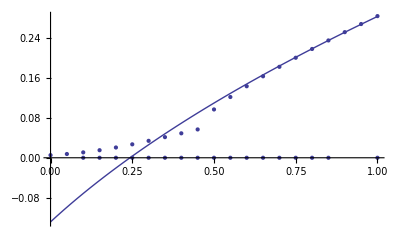

```mathematica
Show[ Plot[twobandinverseug[vgs], {vgs, 0, 1}],ListPlot[Table[{vgs,twobandUanalytcalcal[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1,0.05}]],ListPlot[Table[{vgs,FuncDeltaUParabolicPotentialAnalyticTwoSubbandStrongInversion02[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1,0.05}]]]
```

### unified delta U

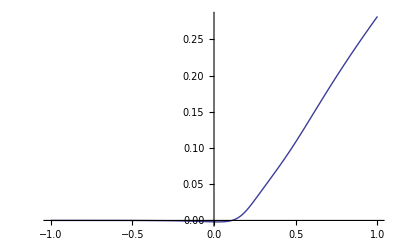

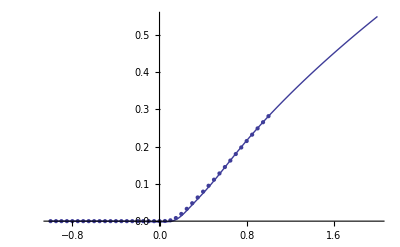

Plot::exclul: {Im[Abs[-43.6547 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, « 6 », (38.6815\ Im[-1.36175\ U + vgs] + Im[-30.2467\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0} 必须是由方程或者实值函数组成的列表.

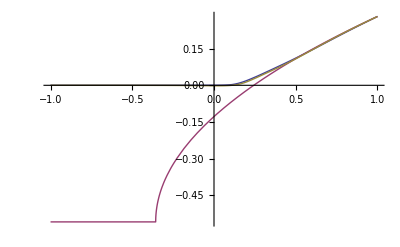

E:\data_for_mathematica\Deltaug\anacalculationfrom2subbandithradius1nm.txt

Plot::exclul: {Im[Abs[-43.6547 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, « 6 », (38.6815\ Im[-1.36175\ U + vgs] + Im[-30.2467\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0} 必须是由方程或者实值函数组成的列表.

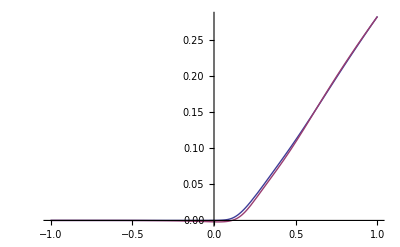

```mathematica
analytictwoSubbandunified[vgs_, vds_, R_, Tox_, st_] := 
 Re[(1/(1 + 
          Exp[a2 ((vgs - wgc + wfb)/vt - st[[2, 3]]/vt - a3)])) allregionuga[
       vgs] + (1/(1 + 
          Exp[-a2 ((vgs - wgc + wfb)/vt - st[[2, 3]]/vt - 
              a3)])) twobandinverseug[vgs] /. a2 -> 0.25 /. a3 -> 5]
Plot[analytictwoSubbandunified[vgs, 1, R, Tox, subbandtable], {vgs, -1, 1}]
Show[Plot[analytictwoSubbandunified[vgs, 1, R, Tox, subbandtable], {vgs, -1, 
   2}], ListPlot[Table[{vgs,twosubbandsnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1,0.05}]]]
Plot[{(*allregionuga[vgs],*)twosubbandsnumugamyrich[vgs,0.8,R,Tox,subbandtable], twobandinverseug[vgs], 
  analytictwoSubbandunified[vgs, 0.8, R, Tox, subbandtable]}, {vgs, -1, 1}]
Export["E:\data_for_mathematica\Deltaug\anacalculationfrom2subbandithradius1nm.txt",Table[{vgs,analytictwoSubbandunified[vgs, 0.8, R, Tox, subbandtable]},{vgs,-1,3,0.01}],"CSV"]
Plot[{twosubbandsnumugamyrich[vgs,0.8,R,Tox,subbandtable],analytictwoSubbandunified[vgs, 0.8, R, Tox, subbandtable]}, {vgs, -1, 1}]
```

```mathematica
subbandtable[[2,3]]
```

0.289918

```mathematica
}
```

## analytic IDS-VGS characteristic

### lowest band

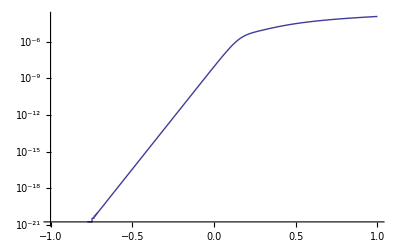

FindRoot::nlnum: 在 {U} = {0.01} 处，函数值 {1.32405×10^-11 - 3.66231×10^-11\ (1/0.56419\ Power[« 2 »] + 0.707107\ Power[« 2 »] + 1/0.56419\ Power[« 2 »] + 0.707107\ Power[« 2 »])} 不是由数字组成的维度为 {1} 的列表.

General::stop: 在本次计算中，FindRoot :: nlnum 的进一步输出将被抑制.

Plot::exclul: {Im[ⅇ^-37.7155 + 38.6815\ (0.  + vgs + Times[« 2 »]) - 30.2467\ Re[Rule[« 2 »]]] - 0, Im[ⅇ^-6.77031 + 38.6815\ (0.  + vgs + Times[« 2 »]) - 30.2467\ Re[Rule[« 2 »]]] - 0} 必须是由方程或者实值函数组成的列表.

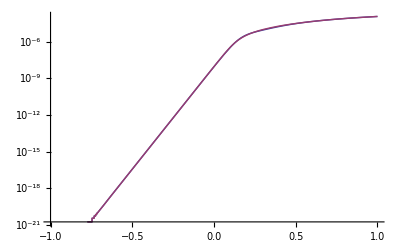

E:\data_for_mathematica\current\anacalculationofcurrentfrom1stsubbandwithradius1nm.txt

E:\data_for_mathematica\current\anacalculationofcurrentfrom1stsubbandwithradius1nm_ua.txt

```mathematica
lowestsubbandanaids[vgs_,vds_,r_,tox_,st_]:=  (e kB T)/(Pi hbar) st[[1,1]] (Log[1+Exp[1/vt(vgs-wgc+wfb-(4 Pi ϵsi allregionuga[vgs])/Cox[r,tox])-st[[1,4]]-st[[1,5]]/vt allregionuga[vgs]]]-Log[1+Exp[1/vt(vgs-wgc+wfb-(4 Pi ϵsi allregionuga[vgs])/Cox[r,tox])-st[[1,4]]-st[[1,5]]/vt allregionuga[vgs]-vds/vt]])
LogPlot[{lowestsubbandanaids[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1}]
LogPlot[{lowestsubbandanaids[vgs,0.8,R,Tox,subbandtable],lowestsubbandnumids[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1}]
Export["E:\data_for_mathematica\current\anacalculationofcurrentfrom1stsubbandwithradius1nm.txt",Table[{vgs,lowestsubbandanaids[vgs, 0.8, R, Tox, subbandtable]},{vgs,-1,3,0.01}],"CSV"]
Export["E:\data_for_mathematica\current\anacalculationofcurrentfrom1stsubbandwithradius1nm_ua.txt",Table[{vgs,10^6 lowestsubbandanaids[vgs, 0.8, R, Tox, subbandtable]},{vgs,-1,3,0.01}],"CSV"]
```

```mathematica
"E:\\data_for_mathematica\\current\\calculationofcurrentfromlowestsubbandwithradius3nm.txt"
```

E:\data_for_mathematica\current\calculationofcurrentfromlowestsubbandwithradius3nm.txt

### 2 bands

Plot::exclul: {Im[Abs[-43.6547 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, (38.6815\ Im[-1.36175\ U + vgs] + Im[-30.2467\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0, « 48 », « 18 »} 必须是由方程或者实值函数组成的列表.

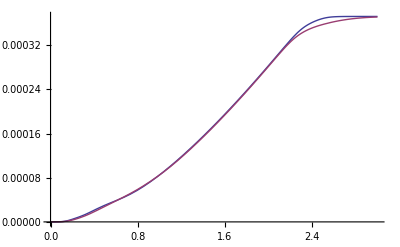

{-0.95,0.}
{-0.925,0.}
{-0.9,0.}
{-0.875,0.}
{-0.85,0.}
{-0.825,0.}
{-0.8,0.}
{-0.775,0.}
{-0.75,1.77907×10^-21}
{-0.725,5.33722×10^-21}
{-0.7,1.60116×10^-20}
{-0.675,4.26977×10^-20}
{-0.65,1.11192×10^-19}
{-0.625,2.93547×10^-19}
{-0.6,7.69449×10^-19}
{-0.575,2.02547×10^-18}
{-0.55,5.32743×10^-18}
{-0.525,1.40102×10^-17}
{-0.5,3.68481×10^-17}
{-0.475,9.69132×10^-17}
{-0.45,2.54897×10^-16}
{-0.425,6.70414×10^-16}
{-0.4,1.76329×10^-15}
{-0.375,4.63769×10^-15}
{-0.35,1.21978×10^-14}
{-0.325,3.20819×10^-14}
{-0.3,8.43798×10^-14}
{-0.275,2.21931×10^-13}
{-0.25,5.83709×10^-13}
{-0.225,1.53524×10^-12}
{-0.2,4.03788×10^-12}
{-0.175,1.06202×10^-11}
{-0.15,2.79323×10^-11}
{-0.125,7.34639×10^-11}
{-0.1,1.93207×10^-10}
{-0.075,5.0807×10^-10}
{-0.05,1.33566×10^-9}
{-0.025,3.50862×10^-9}
{1.11022×10^-16,9.19815×10^-9}
{0.025,2.39886×10^-8}
{0.05,6.17464×10^-8}
{0.075,1.54078×10^-7}
{0.1,3.60543×10^-7}
{0.125,7.59019×10^-7}
{0.15,1.40378×10^-6}
{0.175,2.29981×10^-6}
{0.2,3.42379×10^-6}
{0.225,4.74987×10^-6}
{0.25,6.25681×10^-6}
{0.275,7.92572×10^-6}
{0.3,9.73958×10^-6}
{0.325,0.000011688}
{0.35,0.0000137728}
{0.375,0.0000160021}
{0.4,0.0000183502}
{0.425,0.0000207729}
{0.45,0.0000232305}
{0.475,0.0000256975}
{0.5,0.0000281616}
{0.525,0.0000306188}
{0.55,0.0000330701}
{0.575,0.0000355204}
{0.6,0.0000379763}
{0.625,0.0000404453}
{0.65,0.000042935}
{0.675,0.0000454524}
{0.7,0.0000480064}
{0.725,0.0000506085}
{0.75,0.000053276}
{0.775,0.0000560328}
{0.8,0.0000588919}
{0.825,0.0000618491}
{0.85,0.0000648949}
{0.875,0.0000680204}
{0.9,0.0000712218}
{0.925,0.0000745016}
{0.95,0.0000778663}
{0.975,0.0000813233}
{1.,0.0000848784}
{1.025,0.0000885351}
{1.05,0.0000922944}
{1.075,0.0000961551}
{1.1,0.000100114}
{1.125,0.000104167}
{1.15,0.000108309}
{1.175,0.000112534}
{1.2,0.000116838}
{1.225,0.000121217}
{1.25,0.000125664}
{1.275,0.000130177}
{1.3,0.000134753}
{1.325,0.000139387}
{1.35,0.000144079}
{1.375,0.000148824}
{1.4,0.000153623}
{1.425,0.000158472}
{1.45,0.00016337}
{1.475,0.000168316}
{1.5,0.000173309}

{-0.95,0.}
{-0.925,0.}
{-0.9,0.}
{-0.875,0.}
{-0.85,0.}
{-0.825,0.}
{-0.8,0.}
{-0.775,0.}
{-0.75,1.77907×10^-21}
{-0.725,5.33722×10^-21}
{-0.7,1.60116×10^-20}
{-0.675,4.26977×10^-20}
{-0.65,1.11192×10^-19}
{-0.625,2.93547×10^-19}
{-0.6,7.71228×10^-19}
{-0.575,2.03081×10^-18}
{-0.55,5.347×10^-18}
{-0.525,1.40796×10^-17}
{-0.5,3.70839×10^-17}
{-0.475,9.77057×10^-17}
{-0.45,2.57555×10^-16}
{-0.425,6.79332×10^-16}
{-0.4,1.79321×10^-15}
{-0.375,4.73812×10^-15}
{-0.35,1.24988×10^-14}
{-0.325,3.29511×10^-14}
{-0.3,8.70026×10^-14}
{-0.275,2.2995×10^-13}
{-0.25,6.08384×10^-13}
{-0.225,1.61139×10^-12}
{-0.2,4.27318×10^-12}
{-0.175,1.1347×10^-11}
{-0.15,3.01742×10^-11}
{-0.125,8.03589×10^-11}
{-0.1,2.14316×10^-10}
{-0.075,5.72258×10^-10}
{-0.05,1.52892×10^-9}
{-0.025,4.08225×10^-9}
{1.11022×10^-16,1.08668×10^-8}
{0.025,2.87127×10^-8}
{0.05,7.47009×10^-8}
{0.075,1.88674×10^-7}
{0.1,4.51953×10^-7}
{0.125,9.92877×10^-7}
{0.15,1.92914×10^-6}
{0.175,3.24913×10^-6}
{0.2,4.79719×10^-6}
{0.225,6.42956×10^-6}
{0.25,8.12024×10^-6}
{0.275,9.91953×10^-6}
{0.3,0.0000118786}
{0.325,0.0000140125}
{0.35,0.0000162978}
{0.375,0.0000186843}
{0.4,0.0000211117}
{0.425,0.0000235225}
{0.45,0.0000258724}
{0.475,0.0000281348}
{0.5,0.0000303025}
{0.525,0.0000323853}
{0.55,0.0000344067}
{0.575,0.0000363984}
{0.6,0.0000383952}
{0.625,0.0000404314}
{0.65,0.0000425376}
{0.675,0.000044739}
{0.7,0.0000470552}
{0.725,0.0000494998}
{0.75,0.000052081}
{0.775,0.0000548024}
{0.8,0.0000576638}
{0.825,0.0000606622}
{0.85,0.0000637923}
{0.875,0.0000670477}
{0.9,0.0000704215}
{0.925,0.0000739066}
{0.95,0.0000774959}
{0.975,0.000081183}
{1.,0.000084962}
{1.025,0.0000888276}
{1.05,0.000092775}
{1.075,0.0000968001}
{1.1,0.000100899}
{1.125,0.000105069}
{1.15,0.000109306}
{1.175,0.000113608}
{1.2,0.000117973}
{1.225,0.000122399}
{1.25,0.000126884}
{1.275,0.000131425}
{1.3,0.000136022}
{1.325,0.000140673}
{1.35,0.000145376}
{1.375,0.000150131}
{1.4,0.000154935}
{1.425,0.000159789}
{1.45,0.00016469}
{1.475,0.000169637}
{1.5,0.00017463}

6.77031+30.2467 unideltau

11.2145+30.2467 unideltau

E:\data_for_mathematica\current\analyticcalculationofcurrentfromtwosubbandwithradius1nm.txt

E:\data_for_mathematica\current\analyticcalculationofcurrentfromtwosubbandwithradius1nm_ua.txt

```mathematica
idswithtwobandsana[vgs_,vds_]:=Re[(e kB T)/(Pi hbar) (4 Log[1+Exp[1/vt (vgs-wgc+wfb-4 Pi ϵsi/Cox[R,Tox] analytictwoSubbandunified[vgs,vds,R,Tox,subbandtable])-Eq0]]-4 Log[1+Exp[1/vt (vgs-wgc+wfb-4 Pi ϵsi/Cox[R,Tox] analytictwoSubbandunified[vgs,vds,R,Tox,subbandtable])-Eq0-vds/vt]]+2 Log[1+Exp[1/vt (vgs-wgc+wfb-4 Pi ϵsi/Cox[R,Tox] analytictwoSubbandunified[vgs,vds,R,Tox,subbandtable])-Eq1]]-2 Log[1+Exp[1/vt (vgs-wgc+wfb-4 Pi ϵsi/Cox[R,Tox] analytictwoSubbandunified[vgs,vds,R,Tox,subbandtable])-Eq1-vds/vt]])/.Eq0->subbandtable[[1,4]]+(subbandtable[[1,5]] analytictwoSubbandunified[vgs,vds,R,Tox,subbandtable])/vt/.Eq1->subbandtable[[2,4]]+(subbandtable[[2,5]] analytictwoSubbandunified[vgs,vds,R,Tox,subbandtable])/vt]
Plot[{idswithtwobandsana[vgs,0.8],towsubbandsnumids[vgs,0.8,R,Tox,subbandtable]},{vgs,0,3}]
Column[Table[{vgs,towsubbandsnumids[vgs,0.8,R,Tox,subbandtable]},{vgs,-0.95,1.5,0.025}]]
Column[Table[{vgs,idswithtwobandsana[vgs,0.8]},{vgs,-0.95,1.5,0.025}]]
subbandtable[[1,4]]+(subbandtable[[1,5]] unideltau)/vt
subbandtable[[2,4]]+(subbandtable[[2,5]] unideltau)/vt
Export["E:\data_for_mathematica\current\analyticcalculationofcurrentfromtwosubbandwithradius1nm.txt",Table[{vgs,idswithtwobandsana[vgs,0.8]},{vgs,-1,3,0.01}],"CSV"]
Export["E:\data_for_mathematica\current\analyticcalculationofcurrentfromtwosubbandwithradius1nm_ua.txt",Table[{vgs,10^6 idswithtwobandsana[vgs,0.8]},{vgs,-1,3,0.01}],"CSV"]
```

## analytic IDS-VDS characteristic

Plot::exclul: {Im[Abs[-12.7095 + 38.6815\ Plus[« 2 »] - 30.2467\ U - 38.6815\ vds]^2.82843] - 0, « 34 », Im[ⅇ^-6.77031 - 38.6815\ vds + « 19 »\ (« 1 ») - 6.35327×10^-10\ Re[Plus[« 2 »]]] - 0} 必须是由方程或者实值函数组成的列表.

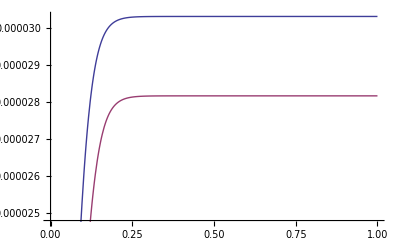

Plot::exclul: {Im[Abs[-12.7095 + 38.6815\ Plus[« 2 »] - 30.2467\ U - 38.6815\ vds]^2.82843] - 0, « 34 », Im[ⅇ^-6.77031 - 38.6815\ vds + « 19 »\ (« 1 ») - 6.35327×10^-10\ Re[Plus[« 2 »]]] - 0} 必须是由方程或者实值函数组成的列表.

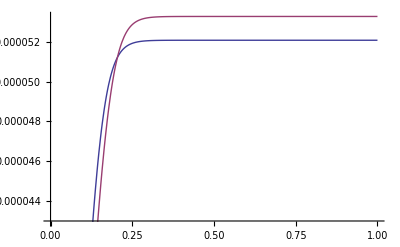

Plot::exclul: {Im[Abs[-12.7095 + 38.6815\ Plus[« 2 »] - 30.2467\ U - 38.6815\ vds]^2.82843] - 0, « 34 », Im[ⅇ^-6.77031 - 38.6815\ vds + « 19 »\ (« 1 ») - 6.35327×10^-10\ Re[Plus[« 2 »]]] - 0} 必须是由方程或者实值函数组成的列表.

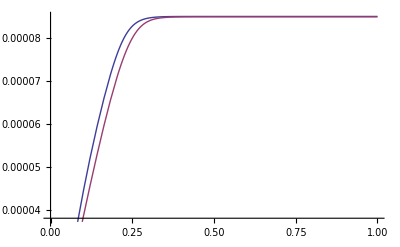

{0.,0.,0.,0.,0.,0.,0.}
{0.01,3.39717×10^-6,2.63982×10^-6,4.24696×10^-6,3.39336×10^-6,4.61744×10^-6,4.0089×10^-6}
{0.02,6.64487×10^-6,5.23053×10^-6,8.36539×10^-6,6.75617×10^-6,9.22046×10^-6,7.98963×10^-6}
{0.03,9.74574×10^-6,7.7594×10^-6,0.0000123357,0.0000100835,0.0000138027,0.000011936}
{0.04,0.000012694,0.0000102105,0.0000161454,0.0000133699,0.0000183554,0.0000158424}
{0.05,0.0000154732,0.0000125651,0.0000197907,0.0000166097,0.0000228665,0.0000197044}
{0.06,0.0000180568,0.0000148029,0.0000232754,0.0000197968,0.0000273205,0.0000235185}
{0.07,0.0000204108,0.000016902,0.0000266068,0.0000229248,0.0000316978,0.0000272824}
{0.08,0.0000225002,0.0000188404,0.0000297907,0.0000259868,0.000035976,0.0000309942}
{0.09,0.0000242971,0.0000205967,0.0000328265,0.0000289721,0.0000401318,0.000034652}
{0.1,0.0000257892,0.000022152,0.0000357038,0.0000318632,0.0000441443,0.0000382531}
{0.11,0.0000269842,0.0000234932,0.0000384018,0.0000346389,0.0000479988,0.0000417951}
{0.12,0.0000279088,0.0000246158,0.0000408899,0.000037276,0.000051689,0.0000452754}
{0.13,0.0000286027,0.0000255259,0.0000431328,0.0000397505,0.000055217,0.0000486914}
{0.14,0.0000291102,0.0000262405,0.0000450976,0.0000420383,0.0000585897,0.0000520399}
{0.15,0.0000294739,0.0000267849,0.0000467623,0.000044116,0.0000618138,0.0000553151}
{0.16,0.0000297306,0.0000271887,0.0000481229,0.0000459631,0.0000648907,0.000058503}
{0.17,0.0000299097,0.0000274815,0.0000491961,0.0000475644,0.0000678131,0.0000615848}
{0.18,0.0000300336,0.0000276901,0.000050015,0.0000489135,0.0000705629,0.0000645402}
{0.19,0.0000301189,0.0000278367,0.0000506223,0.0000500155,0.0000731119,0.0000673483}
{0.2,0.0000301773,0.0000279387,0.0000510623,0.0000508876,0.0000754256,0.0000699874}
{0.21,0.0000302173,0.0000280092,0.0000513753,0.000051557,0.0000774694,0.0000724353}
{0.22,0.0000302445,0.0000280576,0.0000515951,0.0000520568,0.0000792176,0.0000746697}
{0.23,0.000030263,0.0000280907,0.0000517478,0.0000524214,0.0000806608,0.0000766695}
{0.24,0.0000302757,0.0000281133,0.0000518532,0.0000526823,0.00008181,0.0000784178}
{0.25,0.0000302843,0.0000281288,0.0000519256,0.0000528663,0.0000826946,0.0000799053}
{0.26,0.0000302901,0.0000281393,0.0000519751,0.0000529946,0.0000833554,0.0000811335}
{0.27,0.0000302941,0.0000281464,0.0000520089,0.0000530834,0.000083837,0.0000821162}
{0.28,0.0000302967,0.0000281513,0.0000520319,0.0000531445,0.0000841812,0.0000828785}
{0.29,0.0000302986,0.0000281546,0.0000520476,0.0000531864,0.0000844236,0.000083453}
{0.3,0.0000302998,0.0000281568,0.0000520583,0.000053215,0.0000845924,0.0000838754}
{0.31,0.0000303007,0.0000281583,0.0000520656,0.0000532345,0.0000847092,0.0000841796}
{0.32,0.0000303012,0.0000281594,0.0000520705,0.0000532478,0.0000847894,0.0000843951}
{0.33,0.0000303016,0.0000281601,0.0000520739,0.0000532568,0.0000848444,0.0000845459}
{0.34,0.0000303019,0.0000281606,0.0000520761,0.000053263,0.0000848819,0.0000846506}
{0.35,0.0000303021,0.0000281609,0.0000520777,0.0000532671,0.0000849075,0.0000847227}
{0.36,0.0000303022,0.0000281611,0.0000520787,0.00005327,0.000084925,0.0000847722}
{0.37,0.0000303023,0.0000281613,0.0000520794,0.0000532719,0.0000849368,0.0000848061}
{0.38,0.0000303023,0.0000281614,0.0000520799,0.0000532732,0.0000849449,0.0000848292}
{0.39,0.0000303024,0.0000281614,0.0000520803,0.0000532741,0.0000849504,0.0000848449}
{0.4,0.0000303024,0.0000281615,0.0000520805,0.0000532747,0.0000849541,0.0000848556}
{0.41,0.0000303024,0.0000281615,0.0000520806,0.0000532751,0.0000849567,0.0000848629}
{0.42,0.0000303024,0.0000281615,0.0000520807,0.0000532754,0.0000849584,0.0000848679}
{0.43,0.0000303024,0.0000281615,0.0000520808,0.0000532756,0.0000849596,0.0000848712}
{0.44,0.0000303024,0.0000281616,0.0000520809,0.0000532757,0.0000849603,0.0000848735}
{0.45,0.0000303025,0.0000281616,0.0000520809,0.0000532758,0.0000849609,0.0000848751}
{0.46,0.0000303025,0.0000281616,0.0000520809,0.0000532759,0.0000849613,0.0000848761}
{0.47,0.0000303025,0.0000281616,0.0000520809,0.0000532759,0.0000849615,0.0000848769}
{0.48,0.0000303025,0.0000281616,0.0000520809,0.0000532759,0.0000849617,0.0000848773}
{0.49,0.0000303025,0.0000281616,0.0000520809,0.000053276,0.0000849618,0.0000848777}
{0.5,0.0000303025,0.0000281616,0.000052081,0.000053276,0.0000849619,0.0000848779}
{0.51,0.0000303025,0.0000281616,0.000052081,0.000053276,0.0000849619,0.0000848781}
{0.52,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848782}
{0.53,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848782}
{0.54,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848783}
{0.55,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848783}
{0.56,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848783}
{0.57,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848783}
{0.58,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.59,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.6,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.61,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.62,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.63,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.64,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.65,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.66,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.67,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.68,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.69,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.7,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.71,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.72,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.73,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.74,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.75,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.76,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.77,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.78,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.79,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.8,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.81,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.82,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.83,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.84,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.85,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.86,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.87,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.88,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.89,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.9,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.91,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.92,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.93,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.94,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.95,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.96,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.97,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.98,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{0.99,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}
{1.,0.0000303025,0.0000281616,0.000052081,0.000053276,0.000084962,0.0000848784}

E:\data_for_mathematica\numcalcalculationofcurrenttwosubbandwithradiusvd050.txt

E:\data_for_mathematica\numcalcalculationofcurrenttwosubbandwithradiusvd065.txt

E:\data_for_mathematica\numcalcalculationofcurrenttwosubbandwithradiusvd080.txt

E:\data_for_mathematica\numcalcalculationofcurrenttwosubbandwithradiusvd100.txt

E:\data_for_mathematica\anacalcalculationofcurrenttwosubbandwithradiusvd050.txt

E:\data_for_mathematica\anacalcalculationofcurrenttwosubbandwithradiusvd065.txt

E:\data_for_mathematica\anacalcalculationofcurrenttwosubbandwithradiusvd080.txt

E:\data_for_mathematica\anacalcalculationofcurrenttwosubbandwithradiusvd100.txt

```mathematica
Plot[{idswithtwobandsana[0.5,vds],towsubbandsnumids[0.5,vds,R,Tox,subbandtable]},{vds,0,1}]
Plot[{idswithtwobandsana[0.75,vds],towsubbandsnumids[0.75,vds,R,Tox,subbandtable]},{vds,0,1}]
Plot[{idswithtwobandsana[1,vds],towsubbandsnumids[1,vds,R,Tox,subbandtable]},{vds,0,1}]
Column[Table[{vgs,towsubbandsnumids[vgs,0.8,R,Tox,subbandtable]},{vgs,-0.95,1.05,0.05}]];
Column[Table[{vgs,idswithtwobandsana[vgs,0.8]},{vgs,0,1,0.05}]];
Column[Table[{vds,idswithtwobandsana[0.5,vds],towsubbandsnumids[0.5,vds,R,Tox,subbandtable],idswithtwobandsana[0.75,vds],towsubbandsnumids[0.75,vds,R,Tox,subbandtable],idswithtwobandsana[1,vds],towsubbandsnumids[1,vds,R,Tox,subbandtable]},{vds,0,1,0.01}],"CSV"]
Export["E:\data_for_mathematica\\numcalcalculationofcurrenttwosubbandwithradiusvd050.txt",Table[{vds,10^6 towsubbandsnumids[0.5, vds, R, Tox, subbandtable]},{vds,0,1,0.1}],"CSV"]
Export["E:\data_for_mathematica\\numcalcalculationofcurrenttwosubbandwithradiusvd065.txt",Table[{vds,10^6 towsubbandsnumids[0.65, vds, R, Tox, subbandtable]},{vds,0,1,0.1}],"CSV"]
Export["E:\data_for_mathematica\\numcalcalculationofcurrenttwosubbandwithradiusvd080.txt",Table[{vds,10^6 towsubbandsnumids[0.8,vds, R, Tox, subbandtable]},{vds,0,1,0.1}],"CSV"]
Export["E:\data_for_mathematica\\numcalcalculationofcurrenttwosubbandwithradiusvd100.txt",Table[{vds,10^6 towsubbandsnumids[1, vds, R, Tox, subbandtable]},{vds,-1,3,0.1}],"CSV"]
Export["E:\data_for_mathematica\\anacalcalculationofcurrenttwosubbandwithradiusvd050.txt",Table[{vds,10^6 idswithtwobandsana[0.5,vds]},{vds,0,1,0.01}],"CSV"]
Export["E:\data_for_mathematica\\anacalcalculationofcurrenttwosubbandwithradiusvd065.txt",Table[{vds,10^6 idswithtwobandsana[0.65,vds]},{vds,0,1,0.01}],"CSV"]
Export["E:\data_for_mathematica\\anacalcalculationofcurrenttwosubbandwithradiusvd080.txt",Table[{vds,10^6 idswithtwobandsana[0.8,vds]},{vds,0,1,0.01}],"CSV"]
Export["E:\data_for_mathematica\\anacalcalculationofcurrenttwosubbandwithradiusvd100.txt",Table[{vds,10^6 idswithtwobandsana[1,vds]},{vds,0,1,0.01}],"CSV"]
```

```mathematica
subbandtable[[1,5]]
```

0.781943

```mathematica
subbandtable[[2,4]]+(subbandtable[[2,5]] u)/vt
```

11.2145+30.2467 u

```mathematica
subbandtable[[2,3]]
```

0.289918

```mathematica
subbandtable
```

{{4,0.19,0.175027,6.77031,0.781943,0,0.175027},{2,0.916,0.289918,11.2145,0.781943,0,0.289918},{4,0.19,0.444347,17.188,0.666667,0,0.444347},{2,0.916,0.736026,28.4706,0.666667,0,0.736026},{4,0.19,0.922208,35.6724,0.688545,0,0.922208},{2,0.916,1.52756,59.0884,0.688545,0,1.52756},{4,0.19,1.48959,57.6195,0.666667,0,1.48959},{2,0.916,2.46738,95.4421,0.666667,0,1.52756},{4,0.19,2.14426,82.9433,0.638438,0,2.14426},{2,0.916,3.5518,137.389,0.638438,0,3.5518}}

```mathematica
e kB T/(Pi hbar)
```

2.00306×10^-6

## energy calculation

```mathematica
Eq01single[vgs_]:=-ws+(subbandtable[[1,3]]+subbandtable[[1,5]] allregionuga[vgs])/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] allregionuga[vgs]
Eq01Hduble[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[1,3]]+(subbandtable[[1,5]] analytictwoSubbandunified[vgs,vds,R,Tox,subbandtable]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] analytictwoSubbandunified[vgs,vds,R,Tox,subbandtable]
Eq01Ldouble[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[2,3]]+(subbandtable[[2,5]] analytictwoSubbandunified[vgs,vds,R,Tox,subbandtable]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] analytictwoSubbandunified[vgs,vds,R,Tox,subbandtable]
NSeq01single[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[1,3]]+(subbandtable[[1,5]]lowestsubbandnumugamyrich[vgs,vds,R,Tox,subbandtable]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] lowestsubbandnumugamyrich[vgs,vds,R,Tox,subbandtable]
NSeq01H[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[1,3]]+(subbandtable[[1,5]]twosubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] twosubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable]
NSeq01L[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[2,3]]+(subbandtable[[2,5]] twosubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] twosubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable]
```

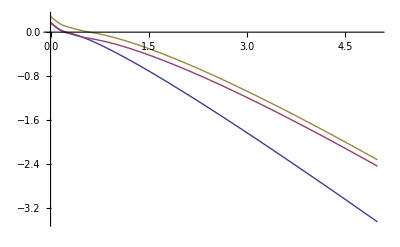

{-1.,1.17503,1.17503,1.28992}
{-0.95,1.12503,1.12503,1.23992}
{-0.9,1.07503,1.07502,1.18991}
{-0.85,1.02503,1.02502,1.13991}
{-0.8,0.975027,0.975018,1.08991}
{-0.75,0.925027,0.925012,1.0399}
{-0.7,0.875027,0.875003,0.989894}
{-0.65,0.825027,0.824988,0.93988}
{-0.6,0.775027,0.774964,0.889855}
{-0.55,0.725027,0.724925,0.839816}
{-0.5,0.675027,0.674862,0.789753}
{-0.45,0.625027,0.624759,0.73965}
{-0.4,0.575027,0.574592,0.689483}
{-0.35,0.525027,0.524397,0.639288}
{-0.3,0.475027,0.474236,0.589127}
{-0.25,0.425028,0.423957,0.538848}
{-0.2,0.375031,0.373563,0.488454}
{-0.15,0.325039,0.323032,0.437923}
{-0.1,0.275068,0.272349,0.38724}
{-0.05,0.225171,0.221551,0.336442}
{0.,0.175527,0.170836,0.285727}
{0.05,0.126741,0.120897,0.235788}
{0.1,0.080672,0.0737562,0.188647}
{0.15,0.0416573,0.0338281,0.148719}
{0.2,0.0143194,0.00540917,0.1203}
{0.25,-0.00364257,-0.0141348,0.100756}
{0.3,-0.0189448,-0.0310273,0.083864}
{0.35,-0.0353406,-0.0478855,0.0670058}
{0.4,-0.0537495,-0.0643464,0.0505449}
{0.45,-0.074119,-0.0793894,0.0355019}
{0.5,-0.096199,-0.092521,0.0223703}
{0.55,-0.119745,-0.104031,0.0108607}
{0.6,-0.144553,-0.114675,0.000215951}
{0.65,-0.17046,-0.125243,-0.0103522}
{0.7,-0.197334,-0.136304,-0.0214131}
{0.75,-0.225067,-0.14817,-0.0332788}
{0.8,-0.253571,-0.160961,-0.0460696}
{0.85,-0.28277,-0.174685,-0.0597934}
{0.9,-0.312601,-0.189295,-0.0744038}
{0.95,-0.343009,-0.204726,-0.0898349}
{1.,-0.373948,-0.22091,-0.106019}

Plot::exclul: {Im[Abs[-43.6547 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, « 6 », (38.6815\ Im[-1.36175\ U + vgs] + Im[-30.2467\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0} 必须是由方程或者实值函数组成的列表.

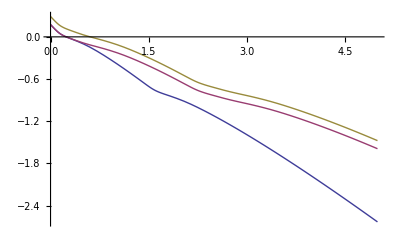

Plot::exclul: {Im[Abs[-43.6547 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, « 6 », (38.6815\ Im[-1.36175\ U + vgs] + Im[-30.2467\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0} 必须是由方程或者实值函数组成的列表.

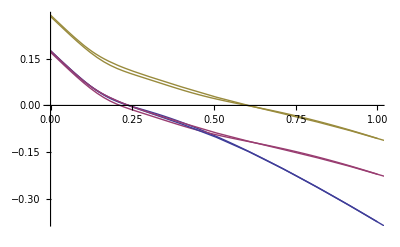

{-1.,1.17503,1.17503,1.28992}
{-0.95,1.12503,1.12503,1.23992}
{-0.9,1.07503,1.07503,1.18992}
{-0.85,1.02503,1.02503,1.13992}
{-0.8,0.975027,0.975027,1.08992}
{-0.75,0.925027,0.925027,1.03992}
{-0.7,0.875027,0.875027,0.989918}
{-0.65,0.825027,0.825027,0.939918}
{-0.6,0.775027,0.775027,0.889918}
{-0.55,0.725027,0.725027,0.839918}
{-0.5,0.675027,0.675027,0.789918}
{-0.45,0.625027,0.625027,0.739918}
{-0.4,0.575027,0.575027,0.689918}
{-0.35,0.525027,0.525027,0.639918}
{-0.3,0.475027,0.475027,0.589918}
{-0.25,0.425027,0.425027,0.539918}
{-0.2,0.375027,0.375027,0.489918}
{-0.15,0.325028,0.325028,0.439919}
{-0.1,0.27503,0.27503,0.389921}
{-0.05,0.225045,0.225045,0.339936}
{0.,0.175147,0.175149,0.29004}
{0.05,0.125831,0.125841,0.240733}
{0.1,0.0796921,0.0797449,0.194636}
{0.15,0.042751,0.0429115,0.157803}
{0.2,0.016163,0.0164908,0.131382}
{0.25,-0.00463107,-0.00402836,0.110863}
{0.3,-0.0229323,-0.0218355,0.0930558}
{0.35,-0.0406061,-0.0385297,0.0763615}
{0.4,-0.0591295,-0.0550886,0.0598026}
{0.45,-0.0786101,-0.0711714,0.0437199}
{0.5,-0.0991907,-0.0862716,0.0286197}
{0.55,-0.121342,-0.100348,0.0145437}
{0.6,-0.14521,-0.11358,0.0013111}
{0.65,-0.170615,-0.126234,-0.011343}
{0.7,-0.197273,-0.138581,-0.0236902}
{0.75,-0.224937,-0.150938,-0.0360464}
{0.8,-0.253434,-0.163733,-0.0488419}
{0.85,-0.282648,-0.177129,-0.0622374}
{0.9,-0.312498,-0.191047,-0.076156}
{0.95,-0.342924,-0.205531,-0.09064}
{1.,-0.373878,-0.22073,-0.105838}
{1.05,-0.405319,-0.236749,-0.121858}
{1.1,-0.437211,-0.253607,-0.138716}
{1.15,-0.469523,-0.271254,-0.156363}
{1.2,-0.502227,-0.289613,-0.174722}
{1.25,-0.535298,-0.308603,-0.193712}
{1.3,-0.568709,-0.328156,-0.213265}
{1.35,-0.602426,-0.348218,-0.233326}
{1.4,-0.636382,-0.368748,-0.253857}
{1.45,-0.67037,-0.389715,-0.274824}
{1.5,-0.703731,-0.411094,-0.296203}
{1.55,-0.734761,-0.432865,-0.317973}
{1.6,-0.7612,-0.455009,-0.340118}
{1.65,-0.782672,-0.477513,-0.362622}
{1.7,-0.800741,-0.50036,-0.385469}
{1.75,-0.816983,-0.523539,-0.408648}
{1.8,-0.832459,-0.547036,-0.432145}
{1.85,-0.848153,-0.570838,-0.455947}
{1.9,-0.864569,-0.59493,-0.480039}
{1.95,-0.881602,-0.619292,-0.5044}
{2.,-0.899409,-0.643883,-0.528991}
{2.05,-0.91824,-0.668616,-0.553725}
{2.1,-0.938167,-0.693285,-0.578393}
{2.15,-0.9591,-0.717425,-0.602534}
{2.2,-0.980887,-0.740206,-0.625315}
{2.25,-1.00338,-0.760704,-0.645813}
{2.3,-1.02648,-0.778595,-0.663704}
{2.35,-1.05008,-0.794324,-0.679433}
{2.4,-1.07415,-0.808594,-0.693703}
{2.45,-1.09864,-0.82197,-0.707079}
{2.5,-1.12352,-0.834881,-0.71999}
{2.55,-1.14876,-0.847722,-0.732831}
{2.6,-1.17433,-0.860514,-0.745622}
{2.65,-1.20023,-0.872986,-0.758095}
{2.7,-1.22644,-0.884974,-0.770083}
{2.75,-1.25294,-0.896447,-0.781556}
{2.8,-1.27971,-0.907452,-0.792561}
{2.85,-1.30675,-0.918083,-0.803192}
{2.9,-1.33405,-0.928456,-0.813565}
{2.95,-1.36158,-0.938692,-0.823801}
{3.,-1.38935,-0.948944,-0.834052}
{3.05,-1.41735,-0.959421,-0.84453}
{3.1,-1.44556,-0.970253,-0.855361}
{3.15,-1.47399,-0.981407,-0.866516}
{3.2,-1.50261,-0.992854,-0.877963}
{3.25,-1.53143,-1.00463,-0.889735}
{3.3,-1.56044,-1.01679,-0.901896}
{3.35,-1.58964,-1.02938,-0.914492}
{3.4,-1.61901,-1.04242,-0.927534}
{3.45,-1.64855,-1.0559,-0.941007}
{3.5,-1.67826,-1.06977,-0.954882}
{3.55,-1.70814,-1.08402,-0.969124}
{3.6,-1.73818,-1.09859,-0.983698}
{3.65,-1.76837,-1.11347,-0.998574}
{3.7,-1.79871,-1.12862,-1.01373}
{3.75,-1.82919,-1.14403,-1.02914}
{3.8,-1.85982,-1.15968,-1.04479}
{3.85,-1.89059,-1.17557,-1.06068}
{3.9,-1.9215,-1.19167,-1.07678}
{3.95,-1.95254,-1.20798,-1.09309}
{4.,-1.98371,-1.2245,-1.10961}
{4.05,-2.01501,-1.24121,-1.12632}
{4.1,-2.04643,-1.25811,-1.14322}
{4.15,-2.07798,-1.2752,-1.16031}
{4.2,-2.10964,-1.29247,-1.17758}
{4.25,-2.14142,-1.30991,-1.19502}
{4.3,-2.17332,-1.32753,-1.21263}
{4.35,-2.20533,-1.34531,-1.23042}
{4.4,-2.23745,-1.36326,-1.24836}
{4.45,-2.26967,-1.38136,-1.26647}
{4.5,-2.302,-1.39963,-1.28473}
{4.55,-2.33444,-1.41804,-1.30315}
{4.6,-2.36698,-1.43661,-1.32172}
{4.65,-2.39962,-1.45533,-1.34043}
{4.7,-2.43235,-1.47419,-1.35929}
{4.75,-2.46519,-1.49319,-1.3783}
{4.8,-2.49811,-1.51233,-1.39744}
{4.85,-2.53113,-1.53161,-1.41671}
{4.9,-2.56425,-1.55102,-1.43613}
{4.95,-2.59745,-1.57056,-1.45567}
{5.,-2.63074,-1.59024,-1.47535}

E:\data_for_mathematica\R2nmEnergyCalculation\NumericalEnergyLevelsingleband.txt

E:\data_for_mathematica\R2nmEnergyCalculation\NumericalEnergyLevelHighersubband.txt

E:\data_for_mathematica\R2nmEnergyCalculation\NumericalEnergyLevelLowersubband.txt

E:\data_for_mathematica\R2nmEnergyCalculation\analyticEnergyLevelLowersubband.txt

E:\data_for_mathematica\R2nmEnergyCalculation\analyticEnergyLevelHighersubband.txt

```mathematica
Plot[{Eq01single[vgs],Eq01Hduble[vgs,0.8,R,Tox,subbandtable],Eq01Ldouble[vgs,0.8,R,Tox,subbandtable]},{vgs,0,5}]
Column[Table[{vgs,Eq01single[vgs],Eq01Hduble[vgs,0.8,R,Tox,subbandtable],Eq01Ldouble[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1,0.05}]]
Plot[{NSeq01single[vgs,0.8,R,Tox,subbandtable],NSeq01H[vgs,0.8,R,Tox,subbandtable],NSeq01L[vgs,0.8,R,Tox,subbandtable]},{vgs,0,5}]
Show[Plot[{Eq01single[vgs],Eq01Hduble[vgs,0.8,R,Tox,subbandtable],Eq01Ldouble[vgs,0.8,R,Tox,subbandtable]},{vgs,0,1}],Plot[{NSeq01single[vgs,0.8,R,Tox,subbandtable],NSeq01H[vgs,0.8,R,Tox,subbandtable],NSeq01L[vgs,0.8,R,Tox,subbandtable]},{vgs,0,5}]]
Column[Table[{vgs,NSeq01single[vgs,0.8,R,Tox,subbandtable],NSeq01H[vgs,0.8,R,Tox,subbandtable],NSeq01L[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.05}]]
Export["E:\data_for_mathematica\R2nmEnergyCalculation\NumericalEnergyLevelsingleband.txt",Table[{vgs,NSeq01single[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.05}]]
Export["E:\data_for_mathematica\R2nmEnergyCalculation\NumericalEnergyLevelHighersubband.txt",Table[{vgs,NSeq01H[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.01}]]
Export["E:\data_for_mathematica\R2nmEnergyCalculation\NumericalEnergyLevelLowersubband.txt",Table[{vgs,NSeq01L[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.01}]]
Export["E:\data_for_mathematica\R2nmEnergyCalculation\analyticEnergyLevelLowersubband.txt",Table[{vgs,Eq01Ldouble[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.1}]]
Export["E:\data_for_mathematica\R2nmEnergyCalculation\analyticEnergyLevelHighersubband.txt",Table[{vgs,Eq01Hduble[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.1}]]
```

## multisubband calculation

Plot::exclul: {Im[Abs[-39.2105 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, (38.6815\ Im[-1.36175\ U + vgs] + Im[-30.2467\ U + « 1 »^« 19 »]) - 0, « 1 », (38.6815\ Im[-1.36175\ U + vgs] + Im[-30.2467\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0} 必须是由方程或者实值函数组成的列表.

Plot::exclul: {Im[Abs[-43.6547 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, « 10 », (38.6815\ Im[-1.36175\ U + vgs] + Im[-25.7877\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0} 必须是由方程或者实值函数组成的列表.

Plot::exclul: {Im[Abs[-43.6547 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, « 18 », (38.6815\ Im[-1.36175\ U + vgs] + Im[-25.7877\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0} 必须是由方程或者实值函数组成的列表.

General::stop: 在本次计算中，Plot :: exclul 的进一步输出将被抑制.

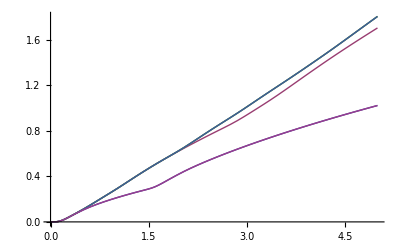

{-1.,8.93211×10^-22,9.04756×10^-22,9.04756×10^-22,9.04756×10^-22,9.04756×10^-22,8.93211×10^-22}
{-0.95,6.17891×10^-21,6.25878×10^-21,6.25878×10^-21,6.25878×10^-21,6.25878×10^-21,6.17891×10^-21}
{-0.9,4.27435×10^-20,4.3296×10^-20,4.3296×10^-20,4.3296×10^-20,4.3296×10^-20,4.27435×10^-20}
{-0.85,2.95684×10^-19,2.99506×10^-19,2.99506×10^-19,2.99506×10^-19,2.99506×10^-19,2.95684×10^-19}
{-0.8,2.04544×10^-18,2.07188×10^-18,2.07188×10^-18,2.07188×10^-18,2.07188×10^-18,2.04544×10^-18}
{-0.75,1.41496×10^-17,1.43325×10^-17,1.43325×10^-17,1.43325×10^-17,1.43325×10^-17,1.41496×10^-17}
{-0.7,9.78819×10^-17,9.91472×10^-17,9.91472×10^-17,9.91472×10^-17,9.91472×10^-17,9.78819×10^-17}
{-0.65,6.77112×10^-16,6.85865×10^-16,6.85865×10^-16,6.85865×10^-16,6.85865×10^-16,6.77112×10^-16}
{-0.6,4.68402×10^-15,4.74457×10^-15,4.74457×10^-15,4.74457×10^-15,4.74457×10^-15,4.68402×10^-15}
{-0.55,3.24024×10^-14,3.28212×10^-14,3.28212×10^-14,3.28212×10^-14,3.28212×10^-14,3.24024×10^-14}
{-0.5,2.24148×10^-13,2.27045×10^-13,2.27045×10^-13,2.27045×10^-13,2.27045×10^-13,2.24148×10^-13}
{-0.45,1.55058×10^-12,1.57062×10^-12,1.57062×10^-12,1.57062×10^-12,1.57062×10^-12,1.55058×10^-12}
{-0.4,1.07263×10^-11,1.0865×10^-11,1.0865×10^-11,1.0865×10^-11,1.0865×10^-11,1.07263×10^-11}
{-0.35,7.42009×10^-11,7.516×10^-11,7.516×10^-11,7.516×10^-11,7.516×10^-11,7.42009×10^-11}
{-0.3,5.13295×10^-10,5.1993×10^-10,5.1993×10^-10,5.1993×10^-10,5.1993×10^-10,5.13295×10^-10}
{-0.25,3.55079×10^-9,3.59669×10^-9,3.59669×10^-9,3.59669×10^-9,3.59669×10^-9,3.55079×10^-9}
{-0.2,2.45631×10^-8,2.48806×10^-8,2.48806×10^-8,2.48806×10^-8,2.48806×10^-8,2.45631×10^-8}
{-0.15,1.69916×10^-7,1.72112×10^-7,1.72112×10^-7,1.72112×10^-7,1.72112×10^-7,1.69916×10^-7}
{-0.1,1.1753×10^-6,1.19049×10^-6,1.19049×10^-6,1.19049×10^-6,1.19049×10^-6,1.1753×10^-6}
{-0.05,8.12481×10^-6,8.22977×10^-6,8.22977×10^-6,8.22977×10^-6,8.22977×10^-6,8.12481×10^-6}
{0.,0.0000559428,0.0000566631,0.0000566631,0.0000566631,0.0000566631,0.0000559428}
{0.05,0.000375121,0.000379848,0.000379848,0.000379848,0.000379848,0.000375121}
{0.1,0.00217615,0.00220082,0.00220082,0.00220082,0.00220082,0.00217615}
{0.15,0.00826793,0.00834294,0.00834294,0.00834294,0.00834294,0.00826793}
{0.2,0.0191893,0.0193425,0.0193425,0.0193425,0.0193425,0.0191893}
{0.25,0.0328134,0.0330953,0.0330953,0.0330953,0.0330953,0.0328134}
{0.3,0.0476004,0.0481135,0.0481135,0.0481135,0.0481135,0.0476004}
{0.35,0.0626801,0.0636516,0.0636516,0.0636516,0.0636516,0.0626801}
{0.4,0.0773635,0.0792543,0.0792543,0.0792543,0.0792543,0.0773635}
{0.45,0.0916003,0.0950813,0.0950813,0.0950813,0.0950813,0.0916003}
{0.5,0.105324,0.11137,0.11137,0.11137,0.11137,0.105324}
{0.55,0.118315,0.128143,0.128143,0.128143,0.128143,0.118315}
{0.6,0.130505,0.145318,0.145318,0.145318,0.145318,0.130505}
{0.65,0.141978,0.16278,0.16278,0.16278,0.16278,0.141978}
{0.7,0.152867,0.180413,0.180413,0.180413,0.180413,0.152867}
{0.75,0.163287,0.198098,0.198098,0.198098,0.198098,0.163287}
{0.8,0.173317,0.215686,0.215686,0.215686,0.215686,0.173317}
{0.85,0.183014,0.233176,0.233176,0.233176,0.233176,0.183014}
{0.9,0.192413,0.250707,0.250707,0.250707,0.250707,0.192413}
{0.95,0.201544,0.26841,0.26841,0.26841,0.26841,0.201544}
{1.,0.210429,0.286367,0.286367,0.286367,0.286367,0.210429}
{1.05,0.219087,0.304607,0.304607,0.304607,0.304607,0.219087}
{1.1,0.227534,0.323102,0.323102,0.323102,0.323102,0.227534}
{1.15,0.235785,0.341781,0.341781,0.341781,0.341781,0.235785}
{1.2,0.243853,0.360558,0.360558,0.360558,0.360558,0.243853}
{1.25,0.25175,0.379324,0.379325,0.379325,0.379325,0.25175}
{1.3,0.259489,0.397931,0.397932,0.397932,0.397932,0.259489}
{1.35,0.267084,0.416325,0.416326,0.416326,0.416326,0.267084}
{1.4,0.274569,0.434533,0.434535,0.434535,0.434535,0.274569}
{1.45,0.282038,0.452548,0.452553,0.452553,0.452553,0.282038}
{1.5,0.2898,0.470329,0.470338,0.470338,0.470338,0.2898}
{1.55,0.298649,0.487843,0.487859,0.487859,0.487859,0.298649}
{1.6,0.30964,0.505081,0.505111,0.505111,0.505111,0.30964}
{1.65,0.322948,0.522056,0.522114,0.522114,0.522114,0.322948}
{1.7,0.337843,0.538789,0.538899,0.538899,0.538899,0.337843}
{1.75,0.353591,0.555304,0.555515,0.555515,0.555515,0.353591}
{1.8,0.369696,0.57162,0.572026,0.572026,0.572026,0.369696}
{1.85,0.385699,0.587756,0.588531,0.588531,0.588531,0.385699}
{1.9,0.401365,0.603725,0.605166,0.605166,0.605166,0.401365}
{1.95,0.416744,0.619536,0.622103,0.622103,0.622103,0.416744}
{2.,0.431762,0.635199,0.63949,0.63949,0.63949,0.431762}
{2.05,0.446302,0.650719,0.657385,0.657385,0.657385,0.446302}
{2.1,0.46033,0.666102,0.675742,0.675742,0.675742,0.46033}
{2.15,0.47389,0.681353,0.694448,0.694448,0.694448,0.47389}
{2.2,0.487051,0.696476,0.713385,0.713385,0.713385,0.487051}
{2.25,0.499881,0.711475,0.732443,0.732443,0.732443,0.499881}
{2.3,0.512432,0.726353,0.751493,0.751493,0.751493,0.512432}
{2.35,0.524743,0.741114,0.770405,0.770405,0.770405,0.524743}
{2.4,0.53684,0.755764,0.789168,0.789168,0.789168,0.53684}
{2.45,0.548741,0.770307,0.807808,0.807808,0.807808,0.548741}
{2.5,0.560461,0.784753,0.826323,0.826323,0.826323,0.560461}
{2.55,0.572012,0.79912,0.844689,0.844689,0.844689,0.572012}
{2.6,0.583405,0.813438,0.862905,0.862905,0.862905,0.583405}
{2.65,0.594646,0.827773,0.881002,0.881002,0.881002,0.594646}
{2.7,0.605746,0.84224,0.89905,0.89905,0.89905,0.605746}
{2.75,0.61671,0.857025,0.917141,0.917141,0.917141,0.61671}
{2.8,0.627544,0.872346,0.935379,0.935379,0.935379,0.627544}
{2.85,0.638255,0.888353,0.953844,0.953844,0.953844,0.638255}
{2.9,0.648847,0.90504,0.972572,0.972572,0.972572,0.648847}
{2.95,0.659325,0.92228,0.991548,0.991548,0.991548,0.659325}
{3.,0.669695,0.939916,1.01072,1.01072,1.01072,0.669695}
{3.05,0.679959,0.957818,1.03004,1.03004,1.03004,0.679959}
{3.1,0.690123,0.975879,1.04943,1.04943,1.04943,0.690123}
{3.15,0.700188,0.993995,1.06883,1.06883,1.06883,0.700188}
{3.2,0.710159,1.01214,1.08815,1.08815,1.08815,0.710159}
{3.25,0.720039,1.03041,1.10736,1.10736,1.10736,0.720039}
{3.3,0.72983,1.04888,1.1265,1.1265,1.1265,0.72983}
{3.35,0.739536,1.06762,1.14557,1.14557,1.14557,0.739536}
{3.4,0.749159,1.08664,1.16459,1.16459,1.16459,0.749159}
{3.45,0.758701,1.10594,1.18356,1.18356,1.18356,0.758701}
{3.5,0.768165,1.12551,1.20249,1.20249,1.20249,0.768165}
{3.55,0.777552,1.14532,1.22144,1.22144,1.22144,0.777552}
{3.6,0.786866,1.16533,1.24044,1.24044,1.24044,0.786866}
{3.65,0.796107,1.18549,1.25952,1.25952,1.25952,0.796107}
{3.7,0.805278,1.20577,1.27871,1.27871,1.27871,0.805278}
{3.75,0.81438,1.22611,1.29801,1.29801,1.29801,0.81438}
{3.8,0.823416,1.24648,1.31741,1.31741,1.31741,0.823416}
{3.85,0.832386,1.26681,1.33692,1.33692,1.33692,0.832386}
{3.9,0.841293,1.28707,1.3565,1.3565,1.3565,0.841293}
{3.95,0.850137,1.30724,1.37615,1.37615,1.37615,0.850137}
{4.,0.858921,1.32731,1.39587,1.39587,1.39587,0.858921}
{4.05,0.867645,1.34731,1.41563,1.41563,1.41563,0.867645}
{4.1,0.876311,1.36722,1.43544,1.43544,1.43544,0.876311}
{4.15,0.88492,1.38704,1.45533,1.45533,1.45533,0.88492}
{4.2,0.893473,1.40674,1.47534,1.47534,1.47534,0.893473}
{4.25,0.901972,1.42631,1.4955,1.4955,1.4955,0.901972}
{4.3,0.910417,1.44575,1.51581,1.51581,1.51581,0.910417}
{4.35,0.91881,1.46504,1.53627,1.53627,1.53627,0.91881}
{4.4,0.927152,1.4842,1.55686,1.55686,1.55686,0.927152}
{4.45,0.935443,1.50322,1.57755,1.57755,1.57755,0.935443}
{4.5,0.943685,1.52212,1.59834,1.59834,1.59834,0.943685}
{4.55,0.951878,1.54091,1.61919,1.61919,1.61919,0.951878}
{4.6,0.960024,1.55959,1.64009,1.64009,1.64009,0.960024}
{4.65,0.968123,1.57816,1.661,1.661,1.661,0.968123}
{4.7,0.976176,1.59665,1.68191,1.68191,1.68191,0.976176}
{4.75,0.984184,1.61504,1.7028,1.7028,1.7028,0.984184}
{4.8,0.992148,1.63335,1.72366,1.72367,1.72367,0.992148}
{4.85,1.00007,1.65158,1.74451,1.74452,1.74452,1.00007}
{4.9,1.00795,1.66974,1.76534,1.76535,1.76535,1.00795}
{4.95,1.01578,1.68782,1.78613,1.78614,1.78614,1.01578}
{5.,1.02358,1.70583,1.80688,1.8069,1.8069,1.02358}

```mathematica
multisubbandnumugamyrich[vgs_,vds_,r_,tox_,st_,j_]:=Re[FindRoot[4 Pi ϵsi U==e/(Pi hbar) Sqrt[(kB T m0)/2] Sum[st[[i,1]] Sqrt[st[[i,2]]](fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-st[[i,4]]-st[[i,5]] U/vt]+fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-st[[i,4]]-st[[i,5]] U/vt-vds/vt]) ,{i,1,2 j-1}],{U,0.01}][[1,2]]]
Plot[{multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,1],multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,2],multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,3],multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,4],multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,5],lowestsubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,0,5}]
Column[Table[{vgs,multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,1],multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,2],multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,3],multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,4],multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,5],lowestsubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.05}]]
for wire radius with 2nanometer(*Export["E:\data_for_mathematica\DeltaUgCalculation\singleband.txt",Table[{vgs,lowestsubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.05}]]
Export["E:\data_for_mathematica\DeltaUgCalculation\2subbands.txt",Table[{vgs,twosubbandsnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.05}]]
```

## five subbands model

```mathematica
multieachsubbandsnumugamyrich[vgs_,vds_,r_,tox_,st_,j_]:=Re[FindRoot[4 Pi ϵsi U==e/(Pi hbar) Sqrt[(kB T m0)/2] Sum[st[[i,1]] Sqrt[st[[i,2]]](fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-st[[i,4]]-st[[i,5]] U/vt]+fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-st[[i,4]]-st[[i,5]] U/vt-vds/vt]) ,{i,1,2 j}],{U,0.01}][[1,2]]]
```

Plot::exclul: {Im[Abs[-43.6547 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, « 38 », (38.6815\ Im[-1.36175\ U + vgs] + Im[-24.6957\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0} 必须是由方程或者实值函数组成的列表.

General::stop: 在本次计算中，Plot :: exclul 的进一步输出将被抑制.

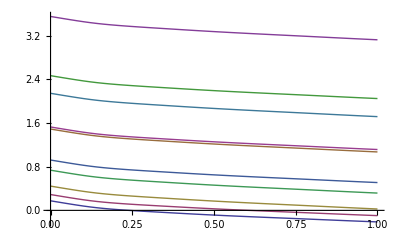

{-1.,1.17503,1.28992,1.44435,1.73603,1.92221,2.52756,2.48959,3.46738,3.14426,4.5518}
{-0.95,1.12503,1.23992,1.39435,1.68603,1.87221,2.47756,2.43959,3.41738,3.09426,4.5018}
{-0.9,1.07503,1.18992,1.34435,1.63603,1.82221,2.42756,2.38959,3.36738,3.04426,4.4518}
{-0.85,1.02503,1.13992,1.29435,1.58603,1.77221,2.37756,2.33959,3.31738,2.99426,4.4018}
{-0.8,0.975027,1.08992,1.24435,1.53603,1.72221,2.32756,2.28959,3.26738,2.94426,4.3518}
{-0.75,0.925027,1.03992,1.19435,1.48603,1.67221,2.27756,2.23959,3.21738,2.89426,4.3018}
{-0.7,0.875027,0.989918,1.14435,1.43603,1.62221,2.22756,2.18959,3.16738,2.84426,4.2518}
{-0.65,0.825027,0.939918,1.09435,1.38603,1.57221,2.17756,2.13959,3.11738,2.79426,4.2018}
{-0.6,0.775027,0.889918,1.04435,1.33603,1.52221,2.12756,2.08959,3.06738,2.74426,4.1518}
{-0.55,0.725027,0.839918,0.994347,1.28603,1.47221,2.07756,2.03959,3.01738,2.69426,4.1018}
{-0.5,0.675027,0.789918,0.944347,1.23603,1.42221,2.02756,1.98959,2.96738,2.64426,4.0518}
{-0.45,0.625027,0.739918,0.894347,1.18603,1.37221,1.97756,1.93959,2.91738,2.59426,4.0018}
{-0.4,0.575027,0.689918,0.844347,1.13603,1.32221,1.92756,1.88959,2.86738,2.54426,3.9518}
{-0.35,0.525027,0.639918,0.794347,1.08603,1.27221,1.87756,1.83959,2.81738,2.49426,3.9018}
{-0.3,0.475027,0.589918,0.744347,1.03603,1.22221,1.82756,1.78959,2.76738,2.44426,3.8518}
{-0.25,0.425027,0.539918,0.694347,0.986026,1.17221,1.77756,1.73959,2.71738,2.39426,3.8018}
{-0.2,0.375027,0.489918,0.644347,0.936026,1.12221,1.72756,1.68959,2.66738,2.34426,3.7518}
{-0.15,0.325028,0.439919,0.594348,0.886026,1.07221,1.67756,1.63959,2.61738,2.29426,3.7018}
{-0.1,0.27503,0.389921,0.54435,0.836028,1.02221,1.62757,1.58959,2.56739,2.24427,3.6518}
{-0.05,0.225045,0.339936,0.494364,0.786042,0.972224,1.57758,1.5396,2.5174,2.19428,3.60182}
{0.,0.175149,0.29004,0.444462,0.736141,0.922324,1.52768,1.4897,2.4675,2.14438,3.55191}
{0.05,0.125841,0.240733,0.395118,0.686796,0.872986,1.47834,1.44036,2.41815,2.09502,3.50256}
{0.1,0.079745,0.194636,0.348812,0.64049,0.82672,1.43207,1.39405,2.37185,2.04867,3.4562}
{0.15,0.0429118,0.157803,0.31127,0.602949,0.789313,1.39467,1.35651,2.33431,2.01095,3.41849}
{0.2,0.0164916,0.131383,0.283582,0.57526,0.761865,1.36722,1.32882,2.30662,1.98295,3.39049}
{0.25,-0.00402676,0.110864,0.261478,0.553157,0.740063,1.34542,1.30672,2.28451,1.96046,3.368}
{0.3,-0.0218324,0.0930589,0.241941,0.53362,0.720854,1.32621,1.28718,2.26498,1.9405,3.34804}
{0.35,-0.0385236,0.0763677,0.223459,0.515137,0.702712,1.30807,1.2687,2.24649,1.92158,3.32911}
{0.4,-0.0550762,0.059815,0.205108,0.496786,0.684702,1.29006,1.25035,2.22814,1.90279,3.31032}
{0.45,-0.0711478,0.0437434,0.187212,0.47889,0.667152,1.27251,1.23245,2.21025,1.88444,3.29198}
{0.5,-0.0862293,0.0286619,0.170252,0.461931,0.650549,1.2559,1.21549,2.19329,1.86702,3.27456}
{0.55,-0.100274,0.0146168,0.154274,0.445952,0.634938,1.24029,1.19951,2.17731,1.85057,3.25811}
{0.6,-0.113456,0.0014355,0.139113,0.430791,0.620152,1.22551,1.18435,2.16215,1.83493,3.24246}
{0.65,-0.126024,-0.0111324,0.124532,0.41621,0.605954,1.21131,1.16977,2.14757,1.81985,3.22739}
{0.7,-0.138223,-0.0233314,0.1103,0.401978,0.592108,1.19746,1.15554,2.13334,1.80512,3.21266}
{0.75,-0.150312,-0.0354211,0.0961718,0.38785,0.578366,1.18372,1.14141,2.11921,1.7905,3.19803}
{0.8,-0.162608,-0.0477164,0.0818489,0.373527,0.564428,1.16978,1.12709,2.10488,1.77568,3.18321}
{0.85,-0.175116,-0.0602246,0.0673246,0.359003,0.550286,1.15564,1.11257,2.09036,1.76066,3.16819}
{0.9,-0.187534,-0.0726423,0.0528859,0.344564,0.536231,1.14159,1.09813,2.07592,1.74572,3.15326}
{0.95,-0.199584,-0.0846924,0.0387951,0.330473,0.522528,1.12788,1.08404,2.06183,1.73113,3.13867}
{1.,-0.211091,-0.0962,0.0252176,0.316896,0.509343,1.1147,1.07046,2.04825,1.71705,3.12459}

```mathematica
Eq01H[vgs_,vds_,r_,tox_,st_]:=-ws+(subbandtable[[1,3]]+(subbandtable[[1,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq01L[vgs_,vds_,r_,tox_,st_]:=-ws+(subbandtable[[2,3]]+(subbandtable[[2,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq11H[vgs_,vds_,r_,tox_,st_]:=-ws+(subbandtable[[3,3]]+(subbandtable[[3,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq11L[vgs_,vds_,r_,tox_,st_]:=-ws+(subbandtable[[4,3]]+(subbandtable[[4,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq02H[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[5,3]]+(subbandtable[[5,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq02L[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[6,3]]+(subbandtable[[6,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq12H[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[7,3]]+(subbandtable[[7,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq12L[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[8,3]]+(subbandtable[[8,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq22H[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[9,3]]+(subbandtable[[9,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq22L[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[10,3]]+(subbandtable[[10,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Plot[{Eq01H[vgs,0.8,R,Tox,subbandtable],Eq01L[vgs,0.8,R,Tox,subbandtable],Eq11H[vgs,0.8,R,Tox,subbandtable],Eq11L[vgs,0.8,R,Tox,subbandtable],Eq02H[vgs,0.8,R,Tox,subbandtable],Eq02L[vgs,0.8,R,Tox,subbandtable],Eq12H[vgs,0.8,R,Tox,subbandtable],Eq12L[vgs,0.8,R,Tox,subbandtable],Eq22H[vgs,0.8,R,Tox,subbandtable],Eq22L[vgs,0.8,R,Tox,subbandtable]},{vgs,0,1}]
Column[Table[{vgs,Eq01H[vgs,0.8,R,Tox,subbandtable],Eq01L[vgs,0.8,R,Tox,subbandtable],Eq11H[vgs,0.8,R,Tox,subbandtable],Eq11L[vgs,0.8,R,Tox,subbandtable],Eq02H[vgs,0.8,R,Tox,subbandtable],Eq02L[vgs,0.8,R,Tox,subbandtable],Eq12H[vgs,0.8,R,Tox,subbandtable],Eq12L[vgs,0.8,R,Tox,subbandtable],Eq22H[vgs,0.8,R,Tox,subbandtable],Eq22L[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1,0.05}]]
```

## degenerate energy levels test

```mathematica
degeneratebesselelement[νf_,νr_,nf_,nr_]:=1/(2 Pi) Integrate[BesselJ[νf,BesselJZero[νf,νr] ζ]^2 ζ,{ζ,0,1}]^(-.5) Integrate[BesselJ[nf,BesselJZero[nf,nr] ζ]^2 ζ,{ζ,0,1}]^(-.5) Integrate[Exp[I (nf-νf) ϕ],{ϕ,0,2 Pi}] Integrate[BesselJ[νf,BesselJZero[νf,νr] ζ] (1-ζ^2) BesselJ[nf,BesselJZero[nf,nr] ζ] ζ,{ζ,0,1}]
```

### degenerate energy levels were found at the energy levels who have positive and negetive coefficients

```mathematica
{degeneratebesselelement[1,1,1,1],degeneratebesselelement[-1,1,-1,1],degeneratebesselelement[1,1,-1,1]}
```

{0.666667,0.666667,0.}

```mathematica
Plot[{u^4+(2 (c40^2 (c2+h00)+c41^2 (c2+h11)))/c1^2 u^3+1/c1^4(-2 c1^2 (c30 c40^2+c31 c41^2)+(c2 (c40-c41) (c40+c41)+c40^2 h00-c41^2 h11)^2) u^2+-1/c1^4 2 (c30 c40^2-c31 c41^2) (c2 (c40-c41) (c40+c41)+c40^2 h00-c41^2 h11) u+((c30 c40^2-c31 c41^2)^2)/c1^4/.b1->c1^2/.b2->(c2+h00)c40^2+(c2+h11)c41^2/.b3->c30 c40^2+c31 c41^2/.b4->2 c40 c41/.b5->c30 c31/.b6->(c2+h11)c30+(c2+h00)c31/.b7->(c2+h00)(c2+h11)/.c1->(4 π^2 ℏ ChannelPermitivity)/e^2 Sqrt[(kB Temperature)/(2m0)]/.c2->(4 π ChannelPermitivity)/Cox[R,Tox]/.c30->(0-wgc+wfb)/ThermalVoltage-subbandtable[[1,3]]/ThermalVoltage/.c31->(0-wgc+wfb)/ThermalVoltage-subbandtable[[2,3]]/ThermalVoltage/.c40->subbandtable[[1,1]]Sqrt[subbandtable[[1,2]]]/.c41->subbandtable[[2,1]]Sqrt[subbandtable[[2,2]]]/.h00->subbandtable[[1,5]]/.h11->subbandtable[[2,5]],u^4+(2 (c40^2 (c2+h00)+c41^2 (c2+h11)))/c1^2 u^3+1/c1^4(-2 c1^2 (c30 c40^2+c31 c41^2)+(c2 (c40-c41) (c40+c41)+c40^2 h00-c41^2 h11)^2) u^2/.b1->c1^2/.b2->(c2+h00)c40^2+(c2+h11)c41^2/.b3->c30 c40^2+c31 c41^2/.b4->2 c40 c41/.b5->c30 c31/.b6->(c2+h11)c30+(c2+h00)c31/.b7->(c2+h00)(c2+h11)/.c1->(4 π^2 ℏ ChannelPermitivity)/e^2 Sqrt[(kB Temperature)/(2m0)]/.c2->(4 π ChannelPermitivity)/Cox[R,Tox]/.c30->(0-wgc+wfb)/ThermalVoltage-subbandtable[[1,3]]/ThermalVoltage/.c31->(0-wgc+wfb)/ThermalVoltage-subbandtable[[2,3]]/ThermalVoltage/.c40->subbandtable[[1,1]]Sqrt[subbandtable[[1,2]]]/.c41->subbandtable[[2,1]]Sqrt[subbandtable[[2,2]]]/.h00->subbandtable[[1,5]]/.h11->subbandtable[[2,5]]},{u,-5,0.5}]
```

-Graphics-

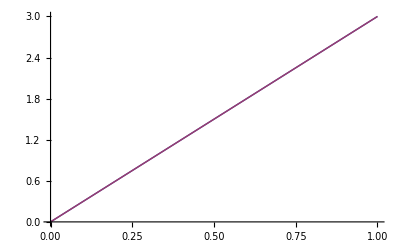

```mathematica
Plot[{x+2 x,x+a x/.a->2},{x,0,1}]
```